```mathematica
(*  Ray Trace Through the IONOSPHERE  Mathematica Notebook  Post Processsing  *)
(*  Copyright (C)2018 Sasan Ardalan                                           *)
(*  This program is free software:you can redistribute it and/or modify       *)
(*  it under the terms of the GNU General Public License as published by      *)
(*  the Free Software Foundation,either version 3 of the License,or           *)
(*  at your option) any later version.This program is distributed             *)
(*  in the hope that it will be useful,but WITHOUT ANY WARRANTY               *)
(*  without even the implied warranty of                                      *)
(*  MERCHANTABILITY or FITNESS FOR A PARTICULAR PURPOSE.See the               *)
(*  GNU General Public License for more details.You should have               *)
(*  received a copy of the GNU General Public License                         *)
(*  along with this program.If not,see<http://www.gnu.org/licenses/>.         *)
(*  Author:Sasan Ardalan                                                      *)
(*  Date:December 28,2018                                                     *)
(*  http://www.radiocalc.com                                                  *)
(*        WORK IN PROGRESS , INCOMPLETE                                       *)

                                                                    
(* The Mathematica Code processes the Ray Matrix computed using               *)
(* The Mathematica Notebook for Ray Tracing which is  based on                *)
(* the FORTRAN Code by :                                                      *)
(* R. Michael Jones, Judith J. Stephenson,   A Versatile Three-Dimensional    *)
(* Ray Tracing Compute Program for Radio Waves in the Ionosphere,             *) 
(* OT Report 75-75, US Department of Commerce,                                *)
(* October 1975                                                                *)
(* Visit http://www.radiocalc.com for details                                  *)

(*  The program reads in the Ray Matrix rayMatrix.wdx                         *)
(* It also reads in and uses the parameters stored in W.wdx                   *)
(*  Translation and Modification of:  *) 
(*           PRINTR FORTRAN Routine                                           *)
(*     Purpose is to generate the ray path ( ray trace) Height versus Range   *)
(*            and other data                                                  *)
(* The Ray path is then plotted ( range versus height)                        *)
(*  This Mathematica Code is semi working but range is off as well as height  *)
(*  due to differences found n ArcTan versus Atan2 (FORTRAN)                  *)
(* and other descrepencies.                                                   *)
(* Ultamately this code needs to be debugged.                                 *)
(* We are providing it as a start. IT IS NOT WORKING PROPERLY                *)
(*                                                                            *)
(*                                                                            *)
(* **************************************************************************)
(* *************** RayPath   ************************************************)
(*   Adopted from PRINTR FORTRAN ROUTINE                                     *)
(*                                                                           *)
(*         Hard Coded for 45 Degree Elevation and 45 Degree Azimuth          *)
(* **************************************************************************)

RayPath[  ]:=
 Module [{R0, SPL, CPL,SP,CP,SL, CL,XR,YR,ZR,CTHR,STHR,PHIR,ALPH,G,G1,NR,NP,PDEV,ABSORB,DOPP,TLOND,TLATD,AZ,EL,NHOP,V,H,STH,CTH,
XP,YP,ZP,EPS,ETA,ZETA,RCE2,RCE, RANGE ,ELL,SR,ANGA,AZDEV,ANA,  SANA, SPHI,CPHI, AZA,
 F,THETA,PHI,AZ1,RCVRH,HOP,BETA,
PLAT,PLON,TLAT,TLON,EARTHR,XMTRH},

(* Print ["RayPath Ray=",Ray]; *)

THETA=Re[Ray[[2]]];
PHI=Re[Ray[[3]]];
F=WPost[[7]];
AZ1=WPost[[10]];

AZ1= 45/DEGS; (* for now*)
BETA=WPost[[14]];

BETA= 45/DEGS; (* for now *)

RCVRH=WPost[[20]];
HOP=WPost[[22]];

PLAT=WPost[[24]];
PLON=WPost[[25]];
TLAT=WPost[[4]];
 TLON=WPost[[5]];

 (* Print["Ray Path Degrees PLAT=",PLAT, " PLON=",PLON];
Print["Ray Path Degrees TLAT=",TLAT, " TLON=",TLON]; *)
PLAT=PLAT/DEGS;
PLON=PLON/DEGS;
TLAT=TLAT/DEGS;
TLON=TLON/DEGS;


 (* Print["Ray Path PLAT=",PLAT, " PLON=",PLON, " AZ1= ", AZ1, "BETA=", BETA]; *)
(* Print["Ray Path THETA=",THETA, " PHI=",PHI, " F= ", F, "AZ1=", AZ1];  *)

 EARTHR=WPost[[2]];
 XMTRH=WPost[[3]];

  (* Print["Ray Path ", "EARTHR= ", EARTHR," XMTRH=", XMTRH];   *)


NWHY="TYPE SPEC";

SPL=Sin[PLON-TLON];
CPL=Cos[ (PLON-TLON)];
SP=Sin[PLAT];
CP=Cos[PLAT];
SL=Sin[ TLAT];
CL=Cos[TLAT];
(**********MATRIX TO ROTATE COORDINATES  *)
G=Table[0,3,3];
G1=Table[0,3,3];
 


G[[1,1]]=CPL*SP*CL-CP*SL;
G[[1,2]]=SPL*SP;
G [[1,3]]=-SL*SP*CPL-CL*CP;
G[[2,1]]=-SPL*CL;
G[[2,2]]=CPL;
G[[2,3]]=SL*SPL;
G [[3,1]]=CL*CP*CPL+SP*SL;
G[[3,2]]=CP*SPL;
G[[3,3]]=-SL*CP*CPL+SP*CL;

  (* Print["G matrix=",G];  *) 


R0=Re[EARTHR+XMTRH];
(*********CARTESIAN COORDINATES OF TRANSMITTER *)
XR=R0*G[[1,1]];
YR=R0*G[[2,1]];
ZR=R0*G[[3,1]];
CTHR=G[[3,1]];
STHR=Sin [ArcCos [CTHR]];
PHIR=ArcTan[YR,XR];
ALPH=ArcTan [G[[3,2]],G[[3,3]]];
G1=Inverse[G];


 (* Print["G1 matrix=",G1];   *)

NR=6;
NP=0;
PDEV=0;
ABSORB=0;
DOPP=0.;
TLOND=TLON*DEGS;
If[TLOND <0., TLOND=TLOND+360.];
TLATD=TLAT*DEGS;
If[TLATD <0., TLATD=TLATD+360.];
AZ=AZ1*DEGS;
EL=BETA*DEGS;
NHOP=HOP;
V=0;

H=Re[Ray[[1]]]-EARTHR;
STH=Sin [THETA];
CTH=Cos [ THETA];

(* PHI=PHI-Pi;  SHA *)
(* PHI=-0.754334; *)
PHI=PHI-Pi; (* Mathematica FORTRAN ArcTan Issue *)

(* Print["R(1)=",Ray[[1]]]; *)


(*********CARTESIAN COORDINATES OF RAY POINT,ORIGIN AT TRANSMITTER  *)
XP=Re[Ray[[1]]]*STH*Cos [PHI]-XR;
YP=Re[Ray[[1]]]*STH*Sin[  PHI]-YR;
ZP=Re[Ray[[1]]]*CTH-ZR;
 (* Print["Raypath ", " XR= ", XR," YR= ",YR," ZR= ",ZR];  
  Print["Raypath ", " XP= ", XP," YP= ",YP," ZP= ",ZP];  *)

(********CARTESIAN COORDINATES OF RAY POINT,ORIGIN AT TRANSMITTER AND  ROTATED *)
EPS=XP*G1[[1,1]]+YP*G1[[1,2]]+ZP*G1[[1,3]];

ETA=XP*G1[[2,1]]+YP*G1[[2,2]]+ZP*G1[[2,3]];
ZETA=XP*G1[[3,1]]+YP*G1[[3,2]]+ZP*G1[[3,3]];
RCE2=ETA^2+ZETA^2;
RCE=Sqrt [RCE2];

(*********GROUND RANGE  Corrected based on Jones *)
RANGE=EARTHR*ArcTan [RCE,(EARTHR+EPS+XMTRH)];
 



  (*Print["RayPath Range RCE,EARTHR,EPS,XMTRH","R0= ",R0," RANGE=",RANGE," RCE- ",  RCE," EARTHR= ",EARTHR," EPS=  ",EPS," XMTRH= ",XMTRH," ArcTan [RCE,EARTHR+EPS+XMTRH]=",ArcTan [RCE,EARTHR+EPS+XMTRH]*DEGS];  *)
 
(**** ANGLE OF WAVE NORMAL WITH LOCAL HORIZONTAL *)
ELL=ArcTan[Re[Ray[[4]]],Sqrt [Re[Ray[[5]]]^2+Re[Ray[[6]]]^2]]*DEGS;

If[ELL > 90., ELL=90-(ELL-90)];
(*********STRAIGHT LINE DISTANCE IE FROM TRANSMITTER TO RAY POINT  *)
SR=Sqrt [RCE2+EPS^2];
ANGA=ArcTan [ETA,ZETA];

AZDEV=180.-Mod[540.-(AZ1-ANGA)*DEGS,360.];
(* IF (R(5).NE.0..OR.R(6).NE.0.) GO TO 34  *) 
(*********WAVE NORMAL IS VERTICAL,SO AZIMUTH DIRECTION CANNOT BE CALCULATED *)
 
 ANA=ANGA-ALPH;

       SANA=Sin [ANA];
        SPHI=SANA*STHR/STH;
    CPHI=-Cos[ANA]*Cos[(PHI-PHIR)]+SANA*Sin [PHI-PHIR]*CTHR;
       AZA=180.-Mod[540.-(ArcTan[SPHI,CPHI]-ArcTan[Re[Ray[[6]]] ,Re[Ray[[5]]]])*DEGS,360.];
      Print["uu  ",ii," V=",V," NWHY=",NWHY," H=",H," Range=",RANGE, " AZDEV*AZA=",AZDEV*AZA," El=",EL," ELL=",ELL," SR=", SR," T=",T];

If[ii >1, AppendTo[CoordinatesRay,{ RANGE,H}];];
 

] (* End RapPath *)




(* ****************************************************************************)
(* *************** PolCar   *************************************)
(***   CONVERTS SPHERICAL COORDINATES TO CARTESIAN   ***)

(*
 * Global
* S
* XO, RO, XXX
* R
*)
(* ****************************************************************************)

PolCarAnalysis[  IENTR_]:=
 Module [{ SINA, COSA,SINP,COSP,TEMP, Done},
Done=False;
If [IENTR==0,
(*  CONVERTS SPHERICAL COORDINATES TO CARTESIAN   *)
If [!(Re[Ray[[5]]]==0.&& Re[Ray[[6]]]==0.),  
VERT=0.;
                 SINA=Sin[Ray[[2]]];
                COSA=Sin[Pi/2-Ray[[2]]];
                SINP=Sin[Ray[[3]]];
                COSP=Sin[Pi/2-Ray[[3]]];
                 XO[[1]]=Ray[[1]]*SINA*COSP;
                 XO[[2]]=Ray[[1]]*SINA*SINP;
                 XO[[3]]=Ray[[1]]*COSA;
    XXX[[4]]=Ray[[4]]*SINA*COSP+Ray[[5]]*COSA*COSP-Ray[[6]]*SINP;
    XXX[[5]]=Ray[[4]]*SINA*SINP+Ray[[5]]*COSA*SINP+Ray[[6]]*COSP;
                 XXX[[6]]=Ray[[4]]*COSA-Ray[[5]]*SINA;
     (*Print["PolCar 0 000000 R(5)=", R[[5]], " R(6)=",R[[6]]];*)
 Return[];
 
];
 
(*  VERTICAL INCIDENCE   *)
VERT=1.;
             RO[[1]]=Ray[[1]];
             RO[[2]]=Ray[[2]];
             RO[[3]]=Ray[[3]];
              RO[[4]]=Sign [Ray[[4]]];

Print["PolCar 0 VERTICAL   1111 R(5)=", R[[5]], " R(6)=",R[[6]]];
Return[];

];
If[ VERT ==0.,
    XXX[[1]]=XO [[1]]+S*XXX[[4]];

     XXX[[2]]=XO[[2]]+S*XXX[[5]];
              XXX[[3]]=XO[[3]]+S*XXX[[6]];
              TEMP=Sqrt[XXX[[1]]^2+XXX[[2]]^2];
               R[[1]]=Sqrt[XXX[[1]]^2+XXX[[2]]^2+XXX[[3]]^2];
      R[[2]]=ArcTan[Re[TEMP],Re[XXX[[3]]]];
                 R[[3]]=ArcTan[Re[XXX[[2]]],Re[XXX[[1]]]];
                 R[[4]]=(XXX[[1]]*XXX[[4]]+XXX[[2]]*XXX[[5]]+XXX[[3]]*XXX[[6]])/Ray[[1]];
                R[[5]]=(XXX[[3]]*(XXX[[1]]*XXX[[4]]+XXX[[2]]*XXX[[5]])-(XXX[[1]]^2 +XXX[[2]]^2)*XXX[[6]])/(Ray[[1]]*TEMP);
                  R[[6]]=(XXX[[1]]*XXX[[5]]-XXX[[2]]*XXX[[4]])/TEMP;
        For [ii=1, ii≤3,ii++,
              XO[[ii]]=XXX[[ii]];
      ];

       Print["PolCar 8888 R(1)=", R[[1]], "  S=",S];

                  Return[];
];

(*  VERTICAL INCIDENCE   *)
R[[1]]=RO[[1]]+RO[[4]]*S;
        R[[2]]=RO[[2]];
        R[[3]]=RO[[3]];
        R[[4]]=RO[[4]];
        R[[5]]=0.;
        R[[6]]=0.;
  Print["PolCar 99999 R(1)=", R[[1]]," RO(1) =",RO[[1]], " RO(4) = ",RO[[4]], "  S= ",S];

 For [ii=1, ii≤4,ii++,
              RO[[ii]]=R[[ii]];
      ];
Return[];


];
```

604

Length Matrix=604

6.28319

1.5708

57.2958

0.0174533

299793.

-4.29124×10^11

-105

40.

XMTRH=0. PLAT=1.37008 PLON=5.07891

TLAT=40. TLON=-105

uu  1 V=0 NWHY=TYPE SPEC H=0. Range=9745.78 AZDEV*AZA=-15556.7 El=45. ELL=45. SR=260.172 T=54165.6

uu  2 V=0 NWHY=TYPE SPEC H=0. Range=9745.78 AZDEV*AZA=-15556.7 El=45. ELL=45. SR=260.172 T=54165.6

uu  3 V=0 NWHY=TYPE SPEC H=79.1872 Range=-63.3072 AZDEV*AZA=-1255.3 El=45. ELL=44.1723 SR=9109.64 T=54165.6

uu  4 V=0 NWHY=TYPE SPEC H=79.5523 Range=-63.0227 AZDEV*AZA=-1255.24 El=45. ELL=44.1785 SR=9109.7 T=54165.6

uu  5 V=0 NWHY=TYPE SPEC H=79.9174 Range=-62.7384 AZDEV*AZA=-1255.17 El=45. ELL=44.186 SR=9109.75 T=54165.6

uu  6 V=0 NWHY=TYPE SPEC H=80.6473 Range=-62.1697 AZDEV*AZA=-1255.04 El=45. ELL=44.2028 SR=9109.87 T=54165.6

uu  7 V=0 NWHY=TYPE SPEC H=81.3764 Range=-61.6013 AZDEV*AZA=-1254.9 El=45. ELL=44.226 SR=9109.99 T=54165.6

uu  8 V=0 NWHY=TYPE SPEC H=82.1051 Range=-61.0332 AZDEV*AZA=-1254.77 El=45. ELL=44.2547 SR=9110.11 T=54165.6

uu  9 V=0 NWHY=TYPE SPEC H=82.8329 Range=-60.4653 AZDEV*AZA=-1254.64 El=45. ELL=44.2904 SR=9110.23 T=54165.6

uu  10 V=0 NWHY=TYPE SPEC H=83.5597 Range=-59.8976 AZDEV*AZA=-1254.51 El=45. ELL=44.3343 SR=9110.35 T=54165.6

uu  11 V=0 NWHY=TYPE SPEC H=84.2854 Range=-59.3303 AZDEV*AZA=-1254.37 El=45. ELL=44.3879 SR=9110.46 T=54165.6

uu  12 V=0 NWHY=TYPE SPEC H=85.0098 Range=-58.7633 AZDEV*AZA=-1254.24 El=45. ELL=44.453 SR=9110.58 T=54165.6

uu  13 V=0 NWHY=TYPE SPEC H=85.7324 Range=-58.1967 AZDEV*AZA=-1254.11 El=45. ELL=44.5315 SR=9110.7 T=54165.6

uu  14 V=0 NWHY=TYPE SPEC H=86.4531 Range=-57.6305 AZDEV*AZA=-1253.98 El=45. ELL=44.6259 SR=9110.81 T=54165.6

uu  15 V=0 NWHY=TYPE SPEC H=87.1714 Range=-57.0647 AZDEV*AZA=-1253.85 El=45. ELL=44.7389 SR=9110.92 T=54165.6

uu  16 V=0 NWHY=TYPE SPEC H=87.887 Range=-56.4995 AZDEV*AZA=-1253.72 El=45. ELL=44.8737 SR=9111.03 T=54165.6

uu  17 V=0 NWHY=TYPE SPEC H=88.5992 Range=-55.9349 AZDEV*AZA=-1253.59 El=45. ELL=45.034 SR=9111.14 T=54165.6

uu  18 V=0 NWHY=TYPE SPEC H=89.3076 Range=-55.3709 AZDEV*AZA=-1253.45 El=45. ELL=45.2241 SR=9111.25 T=54165.6

uu  19 V=0 NWHY=TYPE SPEC H=90.0115 Range=-54.8077 AZDEV*AZA=-1253.32 El=45. ELL=45.4492 SR=9111.35 T=54165.6

uu  20 V=0 NWHY=TYPE SPEC H=90.71 Range=-54.2454 AZDEV*AZA=-1253.19 El=45. ELL=45.715 SR=9111.45 T=54165.6

uu  21 V=0 NWHY=TYPE SPEC H=91.4023 Range=-53.6839 AZDEV*AZA=-1253.06 El=45. ELL=46.0286 SR=9111.55 T=54165.6

uu  22 V=0 NWHY=TYPE SPEC H=92.0875 Range=-53.1236 AZDEV*AZA=-1252.93 El=45. ELL=46.3979 SR=9111.64 T=54165.6

uu  23 V=0 NWHY=TYPE SPEC H=92.7643 Range=-52.5645 AZDEV*AZA=-1252.81 El=45. ELL=46.8324 SR=9111.73 T=54165.6

uu  24 V=0 NWHY=TYPE SPEC H=93.4314 Range=-52.0067 AZDEV*AZA=-1252.68 El=45. ELL=47.3433 SR=9111.81 T=54165.6

uu  25 V=0 NWHY=TYPE SPEC H=94.0873 Range=-51.4504 AZDEV*AZA=-1252.55 El=45. ELL=47.9438 SR=9111.89 T=54165.6

uu  26 V=0 NWHY=TYPE SPEC H=94.7304 Range=-50.8957 AZDEV*AZA=-1252.42 El=45. ELL=48.6494 SR=9111.95 T=54165.6

uu  27 V=0 NWHY=TYPE SPEC H=95.3587 Range=-50.3427 AZDEV*AZA=-1252.29 El=45. ELL=49.4788 SR=9112.01 T=54165.6

uu  28 V=0 NWHY=TYPE SPEC H=95.97 Range=-49.7917 AZDEV*AZA=-1252.17 El=45. ELL=50.4541 SR=9112.06 T=54165.6

uu  29 V=0 NWHY=TYPE SPEC H=96.562 Range=-49.2426 AZDEV*AZA=-1252.04 El=45. ELL=51.6021 SR=9112.09 T=54165.6

uu  30 V=0 NWHY=TYPE SPEC H=97.1318 Range=-48.6954 AZDEV*AZA=-1251.92 El=45. ELL=52.9548 SR=9112.11 T=54165.6

uu  31 V=0 NWHY=TYPE SPEC H=97.6762 Range=-48.1499 AZDEV*AZA=-1251.79 El=45. ELL=54.551 SR=9112.11 T=54165.6

uu  32 V=0 NWHY=TYPE SPEC H=98.191 Range=-47.6056 AZDEV*AZA=-1251.67 El=45. ELL=56.437 SR=9112.09 T=54165.6

uu  33 V=0 NWHY=TYPE SPEC H=98.671 Range=-47.0612 AZDEV*AZA=-1251.54 El=45. ELL=58.668 SR=9112.05 T=54165.6

uu  34 V=0 NWHY=TYPE SPEC H=99.1077 Range=-46.5139 AZDEV*AZA=-1251.42 El=45. ELL=61.3041 SR=9111.97 T=54165.6

uu  35 V=0 NWHY=TYPE SPEC H=99.4856 Range=-45.9574 AZDEV*AZA=-1251.29 El=45. ELL=64.3844 SR=9111.85 T=54165.6

uu  36 V=0 NWHY=TYPE SPEC H=99.786 Range=-45.3849 AZDEV*AZA=-1251.16 El=45. ELL=67.8525 SR=9111.66 T=54165.6

uu  37 V=0 NWHY=TYPE SPEC H=99.846 Range=-45.2389 AZDEV*AZA=-1251.13 El=45. ELL=68.7619 SR=9111.6 T=54165.6

uu  38 V=0 NWHY=TYPE SPEC H=99.904 Range=-45.0929 AZDEV*AZA=-1251.1 El=45. ELL=69.6806 SR=9111.53 T=54165.6

uu  39 V=0 NWHY=TYPE SPEC H=99.9567 Range=-44.9462 AZDEV*AZA=-1251.06 El=45. ELL=70.6089 SR=9111.47 T=54165.6

uu  40 V=0 NWHY=TYPE SPEC H=100.007 Range=-44.7993 AZDEV*AZA=-1251.03 El=45. ELL=71.5473 SR=9111.4 T=54165.6

uu  41 V=0 NWHY=TYPE SPEC H=100.05 Range=-44.652 AZDEV*AZA=-1251. El=45. ELL=72.4893 SR=9111.33 T=54165.6

uu  42 V=0 NWHY=TYPE SPEC H=100.09 Range=-44.5046 AZDEV*AZA=-1250.97 El=45. ELL=73.437 SR=9111.25 T=54165.6

uu  43 V=0 NWHY=TYPE SPEC H=100.128 Range=-44.3571 AZDEV*AZA=-1250.93 El=45. ELL=74.3908 SR=9111.17 T=54165.6

uu  44 V=0 NWHY=TYPE SPEC H=100.16 Range=-44.2096 AZDEV*AZA=-1250.9 El=45. ELL=75.3426 SR=9111.09 T=54165.6

uu  45 V=0 NWHY=TYPE SPEC H=100.189 Range=-44.0621 AZDEV*AZA=-1250.87 El=45. ELL=76.2961 SR=9111.01 T=54165.6

uu  46 V=0 NWHY=TYPE SPEC H=100.202 Range=-43.9883 AZDEV*AZA=-1250.85 El=45. ELL=76.774 SR=9110.96 T=54165.6

uu  47 V=0 NWHY=TYPE SPEC H=100.214 Range=-43.9146 AZDEV*AZA=-1250.84 El=45. ELL=77.2497 SR=9110.92 T=54165.6

uu  48 V=0 NWHY=TYPE SPEC H=100.226 Range=-43.8409 AZDEV*AZA=-1250.82 El=45. ELL=77.7252 SR=9110.87 T=54165.6

uu  49 V=0 NWHY=TYPE SPEC H=100.236 Range=-43.7672 AZDEV*AZA=-1250.8 El=45. ELL=78.201 SR=9110.83 T=54165.6

uu  50 V=0 NWHY=TYPE SPEC H=100.246 Range=-43.6935 AZDEV*AZA=-1250.79 El=45. ELL=78.6747 SR=9110.78 T=54165.6

uu  51 V=0 NWHY=TYPE SPEC H=100.254 Range=-43.6199 AZDEV*AZA=-1250.77 El=45. ELL=79.1476 SR=9110.74 T=54165.6

uu  52 V=0 NWHY=TYPE SPEC H=100.262 Range=-43.5463 AZDEV*AZA=-1250.76 El=45. ELL=79.6204 SR=9110.69 T=54165.6

uu  53 V=0 NWHY=TYPE SPEC H=100.269 Range=-43.4728 AZDEV*AZA=-1250.74 El=45. ELL=80.0905 SR=9110.64 T=54165.6

uu  54 V=0 NWHY=TYPE SPEC H=100.276 Range=-43.3993 AZDEV*AZA=-1250.72 El=45. ELL=80.5594 SR=9110.6 T=54165.6

uu  55 V=0 NWHY=TYPE SPEC H=100.281 Range=-43.3258 AZDEV*AZA=-1250.71 El=45. ELL=81.0278 SR=9110.55 T=54165.6

uu  56 V=0 NWHY=TYPE SPEC H=100.286 Range=-43.2524 AZDEV*AZA=-1250.69 El=45. ELL=81.493 SR=9110.5 T=54165.6

uu  57 V=0 NWHY=TYPE SPEC H=100.29 Range=-43.179 AZDEV*AZA=-1250.68 El=45. ELL=81.9565 SR=9110.45 T=54165.6

uu  58 V=0 NWHY=TYPE SPEC H=100.293 Range=-43.1056 AZDEV*AZA=-1250.66 El=45. ELL=82.4192 SR=9110.4 T=54165.6

uu  59 V=0 NWHY=TYPE SPEC H=100.295 Range=-43.0323 AZDEV*AZA=-1250.65 El=45. ELL=82.8782 SR=9110.35 T=54165.6

uu  60 V=0 NWHY=TYPE SPEC H=100.297 Range=-42.9591 AZDEV*AZA=-1250.63 El=45. ELL=83.3351 SR=9110.3 T=54165.6

uu  61 V=0 NWHY=TYPE SPEC H=100.298 Range=-42.9225 AZDEV*AZA=-1250.62 El=45. ELL=83.5632 SR=9110.27 T=54165.6

uu  62 V=0 NWHY=TYPE SPEC H=100.298 Range=-42.8859 AZDEV*AZA=-1250.61 El=45. ELL=83.79 SR=9110.25 T=54165.6

uu  63 V=0 NWHY=TYPE SPEC H=100.298 Range=-42.8493 AZDEV*AZA=-1250.61 El=45. ELL=84.0163 SR=9110.22 T=54165.6

uu  64 V=0 NWHY=TYPE SPEC H=100.298 Range=-42.7762 AZDEV*AZA=-1250.59 El=45. ELL=84.4678 SR=9110.17 T=54165.6

uu  65 V=0 NWHY=TYPE SPEC H=100.297 Range=-42.7031 AZDEV*AZA=-1250.57 El=45. ELL=84.9154 SR=9110.12 T=54165.6

uu  66 V=0 NWHY=TYPE SPEC H=100.295 Range=-42.6301 AZDEV*AZA=-1250.56 El=45. ELL=85.3605 SR=9110.06 T=54165.6

uu  67 V=0 NWHY=TYPE SPEC H=100.294 Range=-42.5936 AZDEV*AZA=-1250.55 El=45. ELL=85.5824 SR=9110.04 T=54165.6

uu  68 V=0 NWHY=TYPE SPEC H=100.293 Range=-42.5571 AZDEV*AZA=-1250.54 El=45. ELL=85.803 SR=9110.01 T=54165.6

uu  69 V=0 NWHY=TYPE SPEC H=100.292 Range=-42.5206 AZDEV*AZA=-1250.54 El=45. ELL=86.0229 SR=9109.98 T=54165.6

uu  70 V=0 NWHY=TYPE SPEC H=100.29 Range=-42.4842 AZDEV*AZA=-1250.53 El=45. ELL=86.2423 SR=9109.96 T=54165.6

uu  71 V=0 NWHY=TYPE SPEC H=100.288 Range=-42.4477 AZDEV*AZA=-1250.52 El=45. ELL=86.4606 SR=9109.93 T=54165.6

uu  72 V=0 NWHY=TYPE SPEC H=100.286 Range=-42.4113 AZDEV*AZA=-1250.51 El=45. ELL=86.6781 SR=9109.9 T=54165.6

uu  73 V=0 NWHY=TYPE SPEC H=100.284 Range=-42.3749 AZDEV*AZA=-1250.5 El=45. ELL=86.8952 SR=9109.88 T=54165.6

uu  74 V=0 NWHY=TYPE SPEC H=100.282 Range=-42.3385 AZDEV*AZA=-1250.5 El=45. ELL=87.111 SR=9109.85 T=54165.6

uu  75 V=0 NWHY=TYPE SPEC H=100.28 Range=-42.3021 AZDEV*AZA=-1250.49 El=45. ELL=87.3261 SR=9109.82 T=54165.6

uu  76 V=0 NWHY=TYPE SPEC H=100.277 Range=-42.2657 AZDEV*AZA=-1250.48 El=45. ELL=87.5407 SR=9109.79 T=54165.6

uu  77 V=0 NWHY=TYPE SPEC H=100.274 Range=-42.2294 AZDEV*AZA=-1250.47 El=45. ELL=87.754 SR=9109.76 T=54165.6

uu  78 V=0 NWHY=TYPE SPEC H=100.271 Range=-42.193 AZDEV*AZA=-1250.47 El=45. ELL=87.9666 SR=9109.74 T=54165.6

uu  79 V=0 NWHY=TYPE SPEC H=100.27 Range=-42.1748 AZDEV*AZA=-1250.46 El=45. ELL=88.0727 SR=9109.72 T=54165.6

uu  80 V=0 NWHY=TYPE SPEC H=100.268 Range=-42.1567 AZDEV*AZA=-1250.46 El=45. ELL=88.1784 SR=9109.71 T=54165.6

uu  81 V=0 NWHY=TYPE SPEC H=100.267 Range=-42.1385 AZDEV*AZA=-1250.45 El=45. ELL=88.2839 SR=9109.69 T=54165.6

uu  82 V=0 NWHY=TYPE SPEC H=100.263 Range=-42.1022 AZDEV*AZA=-1250.45 El=45. ELL=88.4945 SR=9109.67 T=54165.6

uu  83 V=0 NWHY=TYPE SPEC H=100.26 Range=-42.0659 AZDEV*AZA=-1250.44 El=45. ELL=88.7039 SR=9109.64 T=54165.6

uu  84 V=0 NWHY=TYPE SPEC H=100.256 Range=-42.0296 AZDEV*AZA=-1250.43 El=45. ELL=88.9125 SR=9109.61 T=54165.6

uu  85 V=0 NWHY=TYPE SPEC H=100.254 Range=-42.0115 AZDEV*AZA=-1250.43 El=45. ELL=89.0166 SR=9109.6 T=54165.6

uu  86 V=0 NWHY=TYPE SPEC H=100.252 Range=-41.9933 AZDEV*AZA=-1250.42 El=45. ELL=89.1203 SR=9109.58 T=54165.6

uu  87 V=0 NWHY=TYPE SPEC H=100.25 Range=-41.9752 AZDEV*AZA=-1250.42 El=45. ELL=89.2238 SR=9109.57 T=54165.6

uu  88 V=0 NWHY=TYPE SPEC H=100.248 Range=-41.9571 AZDEV*AZA=-1250.42 El=45. ELL=89.3272 SR=9109.55 T=54165.6

uu  89 V=0 NWHY=TYPE SPEC H=100.246 Range=-41.9389 AZDEV*AZA=-1250.41 El=45. ELL=89.4302 SR=9109.54 T=54165.6

uu  90 V=0 NWHY=TYPE SPEC H=100.244 Range=-41.9208 AZDEV*AZA=-1250.41 El=45. ELL=89.533 SR=9109.52 T=54165.6

uu  91 V=0 NWHY=TYPE SPEC H=100.243 Range=-41.9117 AZDEV*AZA=-1250.41 El=45. ELL=89.5843 SR=9109.52 T=54165.6

uu  92 V=0 NWHY=TYPE SPEC H=100.242 Range=-41.9027 AZDEV*AZA=-1250.4 El=45. ELL=89.6356 SR=9109.51 T=54165.6

uu  93 V=0 NWHY=TYPE SPEC H=100.241 Range=-41.8936 AZDEV*AZA=-1250.4 El=45. ELL=89.6868 SR=9109.5 T=54165.6

uu  94 V=0 NWHY=TYPE SPEC H=100.24 Range=-41.8846 AZDEV*AZA=-1250.4 El=45. ELL=89.738 SR=9109.5 T=54165.6

uu  95 V=0 NWHY=TYPE SPEC H=100.239 Range=-41.8755 AZDEV*AZA=-1250.4 El=45. ELL=89.789 SR=9109.49 T=54165.6

uu  96 V=0 NWHY=TYPE SPEC H=100.238 Range=-41.8665 AZDEV*AZA=-1250.4 El=45. ELL=89.8401 SR=9109.48 T=54165.6

uu  97 V=0 NWHY=TYPE SPEC H=100.237 Range=-41.8619 AZDEV*AZA=-1250.4 El=45. ELL=89.8656 SR=9109.48 T=54165.6

uu  98 V=0 NWHY=TYPE SPEC H=100.237 Range=-41.8574 AZDEV*AZA=-1250.39 El=45. ELL=89.8911 SR=9109.47 T=54165.6

uu  99 V=0 NWHY=TYPE SPEC H=100.236 Range=-41.8529 AZDEV*AZA=-1250.39 El=45. ELL=89.9165 SR=9109.47 T=54165.6

uu  100 V=0 NWHY=TYPE SPEC H=100.236 Range=-41.8483 AZDEV*AZA=-1250.39 El=45. ELL=89.942 SR=9109.47 T=54165.6

uu  101 V=0 NWHY=TYPE SPEC H=100.235 Range=-41.8438 AZDEV*AZA=-1250.39 El=45. ELL=89.9674 SR=9109.46 T=54165.6

uu  102 V=0 NWHY=TYPE SPEC H=100.235 Range=-41.8393 AZDEV*AZA=-1250.39 El=45. ELL=89.9928 SR=9109.46 T=54165.6

uu  103 V=0 NWHY=TYPE SPEC H=100.234 Range=-41.8387 AZDEV*AZA=-1250.39 El=45. ELL=89.996 SR=9109.46 T=54165.6

uu  104 V=0 NWHY=TYPE SPEC H=100.234 Range=-41.8382 AZDEV*AZA=-1250.39 El=45. ELL=89.9992 SR=9109.46 T=54165.6

uu  105 V=0 NWHY=TYPE SPEC H=100.234 Range=-41.8376 AZDEV*AZA=-1250.39 El=45. ELL=89.9976 SR=9109.46 T=54165.6

uu  106 V=0 NWHY=TYPE SPEC H=100.234 Range=-41.8365 AZDEV*AZA=-1250.39 El=45. ELL=89.9913 SR=9109.46 T=54165.6

uu  107 V=0 NWHY=TYPE SPEC H=100.234 Range=-41.8353 AZDEV*AZA=-1250.39 El=45. ELL=89.9849 SR=9109.46 T=54165.6

uu  108 V=0 NWHY=TYPE SPEC H=100.234 Range=-41.8331 AZDEV*AZA=-1250.39 El=45. ELL=89.9722 SR=9109.45 T=54165.6

uu  109 V=0 NWHY=TYPE SPEC H=100.233 Range=-41.8308 AZDEV*AZA=-1250.39 El=45. ELL=89.9596 SR=9109.45 T=54165.6

uu  110 V=0 NWHY=TYPE SPEC H=100.233 Range=-41.8285 AZDEV*AZA=-1250.39 El=45. ELL=89.9469 SR=9109.45 T=54165.6

uu  111 V=0 NWHY=TYPE SPEC H=100.233 Range=-41.824 AZDEV*AZA=-1250.39 El=45. ELL=89.9215 SR=9109.45 T=54165.6

uu  112 V=0 NWHY=TYPE SPEC H=100.232 Range=-41.8195 AZDEV*AZA=-1250.39 El=45. ELL=89.8961 SR=9109.44 T=54165.6

uu  113 V=0 NWHY=TYPE SPEC H=100.231 Range=-41.815 AZDEV*AZA=-1250.39 El=45. ELL=89.8708 SR=9109.44 T=54165.6

uu  114 V=0 NWHY=TYPE SPEC H=100.23 Range=-41.8059 AZDEV*AZA=-1250.38 El=45. ELL=89.8201 SR=9109.43 T=54165.6

uu  115 V=0 NWHY=TYPE SPEC H=100.229 Range=-41.7969 AZDEV*AZA=-1250.38 El=45. ELL=89.7696 SR=9109.43 T=54165.6

uu  116 V=0 NWHY=TYPE SPEC H=100.228 Range=-41.7878 AZDEV*AZA=-1250.38 El=45. ELL=89.719 SR=9109.42 T=54165.6

uu  117 V=0 NWHY=TYPE SPEC H=100.226 Range=-41.7697 AZDEV*AZA=-1250.38 El=45. ELL=89.6181 SR=9109.4 T=54165.6

uu  118 V=0 NWHY=TYPE SPEC H=100.223 Range=-41.7516 AZDEV*AZA=-1250.37 El=45. ELL=89.5175 SR=9109.39 T=54165.6

uu  119 V=0 NWHY=TYPE SPEC H=100.221 Range=-41.7335 AZDEV*AZA=-1250.37 El=45. ELL=89.4171 SR=9109.37 T=54165.6

uu  120 V=0 NWHY=TYPE SPEC H=100.218 Range=-41.7154 AZDEV*AZA=-1250.36 El=45. ELL=89.3169 SR=9109.36 T=54165.6

uu  121 V=0 NWHY=TYPE SPEC H=100.216 Range=-41.6974 AZDEV*AZA=-1250.36 El=45. ELL=89.217 SR=9109.35 T=54165.6

uu  122 V=0 NWHY=TYPE SPEC H=100.213 Range=-41.6793 AZDEV*AZA=-1250.36 El=45. ELL=89.1173 SR=9109.33 T=54165.6

uu  123 V=0 NWHY=TYPE SPEC H=100.211 Range=-41.6612 AZDEV*AZA=-1250.35 El=45. ELL=89.0178 SR=9109.32 T=54165.6

uu  124 V=0 NWHY=TYPE SPEC H=100.208 Range=-41.6431 AZDEV*AZA=-1250.35 El=45. ELL=88.9187 SR=9109.3 T=54165.6

uu  125 V=0 NWHY=TYPE SPEC H=100.205 Range=-41.625 AZDEV*AZA=-1250.35 El=45. ELL=88.8197 SR=9109.29 T=54165.6

uu  126 V=0 NWHY=TYPE SPEC H=100.2 Range=-41.5889 AZDEV*AZA=-1250.34 El=45. ELL=88.6223 SR=9109.26 T=54165.6

uu  127 V=0 NWHY=TYPE SPEC H=100.194 Range=-41.5528 AZDEV*AZA=-1250.33 El=45. ELL=88.4262 SR=9109.23 T=54165.6

uu  128 V=0 NWHY=TYPE SPEC H=100.188 Range=-41.5167 AZDEV*AZA=-1250.32 El=45. ELL=88.231 SR=9109.2 T=54165.6

uu  129 V=0 NWHY=TYPE SPEC H=100.185 Range=-41.4986 AZDEV*AZA=-1250.32 El=45. ELL=88.1336 SR=9109.18 T=54165.6

uu  130 V=0 NWHY=TYPE SPEC H=100.183 Range=-41.4806 AZDEV*AZA=-1250.32 El=45. ELL=88.0366 SR=9109.17 T=54165.6

uu  131 V=0 NWHY=TYPE SPEC H=100.18 Range=-41.4625 AZDEV*AZA=-1250.31 El=45. ELL=87.9399 SR=9109.15 T=54165.6

uu  132 V=0 NWHY=TYPE SPEC H=100.173 Range=-41.4264 AZDEV*AZA=-1250.3 El=45. ELL=87.7469 SR=9109.12 T=54165.6

uu  133 V=0 NWHY=TYPE SPEC H=100.167 Range=-41.3904 AZDEV*AZA=-1250.3 El=45. ELL=87.5552 SR=9109.09 T=54165.6

uu  134 V=0 NWHY=TYPE SPEC H=100.161 Range=-41.3543 AZDEV*AZA=-1250.29 El=45. ELL=87.3644 SR=9109.06 T=54165.6

uu  135 V=0 NWHY=TYPE SPEC H=100.154 Range=-41.3183 AZDEV*AZA=-1250.28 El=45. ELL=87.1743 SR=9109.03 T=54165.6

uu  136 V=0 NWHY=TYPE SPEC H=100.148 Range=-41.2822 AZDEV*AZA=-1250.27 El=45. ELL=86.9856 SR=9109. T=54165.6

uu  137 V=0 NWHY=TYPE SPEC H=100.141 Range=-41.2462 AZDEV*AZA=-1250.27 El=45. ELL=86.7978 SR=9108.97 T=54165.6

uu  138 V=0 NWHY=TYPE SPEC H=100.134 Range=-41.2102 AZDEV*AZA=-1250.26 El=45. ELL=86.6106 SR=9108.94 T=54165.6

uu  139 V=0 NWHY=TYPE SPEC H=100.127 Range=-41.1742 AZDEV*AZA=-1250.25 El=45. ELL=86.4249 SR=9108.91 T=54165.6

uu  140 V=0 NWHY=TYPE SPEC H=100.12 Range=-41.1382 AZDEV*AZA=-1250.24 El=45. ELL=86.2402 SR=9108.88 T=54165.6

uu  141 V=0 NWHY=TYPE SPEC H=100.113 Range=-41.1022 AZDEV*AZA=-1250.24 El=45. ELL=86.056 SR=9108.85 T=54165.6

uu  142 V=0 NWHY=TYPE SPEC H=100.105 Range=-41.0663 AZDEV*AZA=-1250.23 El=45. ELL=85.8733 SR=9108.82 T=54165.6

uu  143 V=0 NWHY=TYPE SPEC H=100.098 Range=-41.0303 AZDEV*AZA=-1250.22 El=45. ELL=85.6916 SR=9108.79 T=54165.6

uu  144 V=0 NWHY=TYPE SPEC H=100.082 Range=-40.9584 AZDEV*AZA=-1250.21 El=45. ELL=85.3302 SR=9108.72 T=54165.6

uu  145 V=0 NWHY=TYPE SPEC H=100.066 Range=-40.8866 AZDEV*AZA=-1250.19 El=45. ELL=84.9739 SR=9108.66 T=54165.6

uu  146 V=0 NWHY=TYPE SPEC H=100.05 Range=-40.8148 AZDEV*AZA=-1250.18 El=45. ELL=84.6215 SR=9108.6 T=54165.6

uu  147 V=0 NWHY=TYPE SPEC H=100.041 Range=-40.7789 AZDEV*AZA=-1250.17 El=45. ELL=84.4462 SR=9108.57 T=54165.6

uu  148 V=0 NWHY=TYPE SPEC H=100.033 Range=-40.7431 AZDEV*AZA=-1250.16 El=45. ELL=84.2726 SR=9108.54 T=54165.6

uu  149 V=0 NWHY=TYPE SPEC H=100.024 Range=-40.7072 AZDEV*AZA=-1250.15 El=45. ELL=84.1 SR=9108.5 T=54165.6

uu  150 V=0 NWHY=TYPE SPEC H=100.006 Range=-40.6355 AZDEV*AZA=-1250.14 El=45. ELL=83.7567 SR=9108.44 T=54165.6

uu  151 V=0 NWHY=TYPE SPEC H=99.9882 Range=-40.5639 AZDEV*AZA=-1250.12 El=45. ELL=83.4186 SR=9108.38 T=54165.6

uu  152 V=0 NWHY=TYPE SPEC H=99.9696 Range=-40.4922 AZDEV*AZA=-1250.11 El=45. ELL=83.0842 SR=9108.31 T=54165.6

uu  153 V=0 NWHY=TYPE SPEC H=99.9602 Range=-40.4564 AZDEV*AZA=-1250.1 El=45. ELL=82.918 SR=9108.28 T=54165.6

uu  154 V=0 NWHY=TYPE SPEC H=99.9505 Range=-40.4207 AZDEV*AZA=-1250.09 El=45. ELL=82.7535 SR=9108.25 T=54165.6

uu  155 V=0 NWHY=TYPE SPEC H=99.9408 Range=-40.3849 AZDEV*AZA=-1250.09 El=45. ELL=82.5898 SR=9108.22 T=54165.6

uu  156 V=0 NWHY=TYPE SPEC H=99.9211 Range=-40.3134 AZDEV*AZA=-1250.07 El=45. ELL=82.2645 SR=9108.15 T=54165.6

uu  157 V=0 NWHY=TYPE SPEC H=99.9009 Range=-40.2419 AZDEV*AZA=-1250.06 El=45. ELL=81.9443 SR=9108.09 T=54165.6

uu  158 V=0 NWHY=TYPE SPEC H=99.8802 Range=-40.1704 AZDEV*AZA=-1250.04 El=45. ELL=81.6278 SR=9108.02 T=54165.6

uu  159 V=0 NWHY=TYPE SPEC H=99.8593 Range=-40.099 AZDEV*AZA=-1250.03 El=45. ELL=81.3139 SR=9107.96 T=54165.6

uu  160 V=0 NWHY=TYPE SPEC H=99.8377 Range=-40.0276 AZDEV*AZA=-1250.01 El=45. ELL=81.0054 SR=9107.89 T=54165.6

uu  161 V=0 NWHY=TYPE SPEC H=99.8157 Range=-39.9563 AZDEV*AZA=-1250. El=45. ELL=80.7005 SR=9107.82 T=54165.6

uu  162 V=0 NWHY=TYPE SPEC H=99.7935 Range=-39.8849 AZDEV*AZA=-1249.98 El=45. ELL=80.3982 SR=9107.76 T=54165.6

uu  163 V=0 NWHY=TYPE SPEC H=99.7707 Range=-39.8137 AZDEV*AZA=-1249.97 El=45. ELL=80.1012 SR=9107.69 T=54165.6

uu  164 V=0 NWHY=TYPE SPEC H=99.7476 Range=-39.7424 AZDEV*AZA=-1249.95 El=45. ELL=79.8077 SR=9107.62 T=54165.6

uu  165 V=0 NWHY=TYPE SPEC H=99.7241 Range=-39.6712 AZDEV*AZA=-1249.94 El=45. ELL=79.5168 SR=9107.55 T=54165.6

uu  166 V=0 NWHY=TYPE SPEC H=99.7002 Range=-39.6 AZDEV*AZA=-1249.92 El=45. ELL=79.231 SR=9107.49 T=54165.6

uu  167 V=0 NWHY=TYPE SPEC H=99.6758 Range=-39.5288 AZDEV*AZA=-1249.91 El=45. ELL=78.9487 SR=9107.42 T=54165.6

uu  168 V=0 NWHY=TYPE SPEC H=99.6512 Range=-39.4576 AZDEV*AZA=-1249.89 El=45. ELL=78.6688 SR=9107.35 T=54165.6

uu  169 V=0 NWHY=TYPE SPEC H=99.6261 Range=-39.3865 AZDEV*AZA=-1249.88 El=45. ELL=78.3939 SR=9107.28 T=54165.6

uu  170 V=0 NWHY=TYPE SPEC H=99.6006 Range=-39.3154 AZDEV*AZA=-1249.86 El=45. ELL=78.1224 SR=9107.21 T=54165.6

uu  171 V=0 NWHY=TYPE SPEC H=99.5749 Range=-39.2443 AZDEV*AZA=-1249.85 El=45. ELL=77.8533 SR=9107.14 T=54165.6

uu  172 V=0 NWHY=TYPE SPEC H=99.5487 Range=-39.1733 AZDEV*AZA=-1249.83 El=45. ELL=77.589 SR=9107.08 T=54165.6

uu  173 V=0 NWHY=TYPE SPEC H=99.5221 Range=-39.1022 AZDEV*AZA=-1249.82 El=45. ELL=77.328 SR=9107.01 T=54165.6

uu  174 V=0 NWHY=TYPE SPEC H=99.4953 Range=-39.0312 AZDEV*AZA=-1249.8 El=45. ELL=77.0693 SR=9106.94 T=54165.6

uu  175 V=0 NWHY=TYPE SPEC H=99.468 Range=-38.9602 AZDEV*AZA=-1249.79 El=45. ELL=76.8154 SR=9106.87 T=54165.6

uu  176 V=0 NWHY=TYPE SPEC H=99.4404 Range=-38.8893 AZDEV*AZA=-1249.77 El=45. ELL=76.5645 SR=9106.8 T=54165.6

uu  177 V=0 NWHY=TYPE SPEC H=99.3845 Range=-38.7474 AZDEV*AZA=-1249.74 El=45. ELL=76.07 SR=9106.66 T=54165.6

uu  178 V=0 NWHY=TYPE SPEC H=99.3269 Range=-38.6056 AZDEV*AZA=-1249.71 El=45. ELL=75.5919 SR=9106.51 T=54165.6

uu  179 V=0 NWHY=TYPE SPEC H=99.2681 Range=-38.4638 AZDEV*AZA=-1249.69 El=45. ELL=75.1258 SR=9106.37 T=54165.6

uu  180 V=0 NWHY=TYPE SPEC H=99.2384 Range=-38.393 AZDEV*AZA=-1249.67 El=45. ELL=74.8958 SR=9106.3 T=54165.6

uu  181 V=0 NWHY=TYPE SPEC H=99.2082 Range=-38.3221 AZDEV*AZA=-1249.66 El=45. ELL=74.6708 SR=9106.23 T=54165.6

uu  182 V=0 NWHY=TYPE SPEC H=99.1777 Range=-38.2513 AZDEV*AZA=-1249.64 El=45. ELL=74.4485 SR=9106.16 T=54165.6

uu  183 V=0 NWHY=TYPE SPEC H=99.1161 Range=-38.1097 AZDEV*AZA=-1249.61 El=45. ELL=74.0102 SR=9106.01 T=54165.6

uu  184 V=0 NWHY=TYPE SPEC H=99.0529 Range=-37.9682 AZDEV*AZA=-1249.58 El=45. ELL=73.5867 SR=9105.87 T=54165.6

uu  185 V=0 NWHY=TYPE SPEC H=98.9887 Range=-37.8267 AZDEV*AZA=-1249.55 El=45. ELL=73.1739 SR=9105.72 T=54165.6

uu  186 V=0 NWHY=TYPE SPEC H=98.9563 Range=-37.756 AZDEV*AZA=-1249.54 El=45. ELL=72.9702 SR=9105.65 T=54165.6

uu  187 V=0 NWHY=TYPE SPEC H=98.9235 Range=-37.6853 AZDEV*AZA=-1249.52 El=45. ELL=72.7709 SR=9105.57 T=54165.6

uu  188 V=0 NWHY=TYPE SPEC H=98.8904 Range=-37.6146 AZDEV*AZA=-1249.51 El=45. ELL=72.5741 SR=9105.5 T=54165.6

uu  189 V=0 NWHY=TYPE SPEC H=98.8237 Range=-37.4732 AZDEV*AZA=-1249.48 El=45. ELL=72.186 SR=9105.35 T=54165.6

uu  190 V=0 NWHY=TYPE SPEC H=98.7556 Range=-37.3318 AZDEV*AZA=-1249.45 El=45. ELL=71.8111 SR=9105.2 T=54165.6

uu  191 V=0 NWHY=TYPE SPEC H=98.6865 Range=-37.1905 AZDEV*AZA=-1249.42 El=45. ELL=71.4456 SR=9105.05 T=54165.6

uu  192 V=0 NWHY=TYPE SPEC H=98.6168 Range=-37.0492 AZDEV*AZA=-1249.39 El=45. ELL=71.0868 SR=9104.9 T=54165.6

uu  193 V=0 NWHY=TYPE SPEC H=98.5457 Range=-36.908 AZDEV*AZA=-1249.36 El=45. ELL=70.7412 SR=9104.75 T=54165.6

uu  194 V=0 NWHY=TYPE SPEC H=98.4737 Range=-36.7668 AZDEV*AZA=-1249.33 El=45. ELL=70.4042 SR=9104.6 T=54165.6

uu  195 V=0 NWHY=TYPE SPEC H=98.4011 Range=-36.6255 AZDEV*AZA=-1249.3 El=45. ELL=70.0733 SR=9104.45 T=54165.6

uu  196 V=0 NWHY=TYPE SPEC H=98.3272 Range=-36.4844 AZDEV*AZA=-1249.27 El=45. ELL=69.7546 SR=9104.29 T=54165.6

uu  197 V=0 NWHY=TYPE SPEC H=98.2524 Range=-36.3432 AZDEV*AZA=-1249.24 El=45. ELL=69.4437 SR=9104.14 T=54165.6

uu  198 V=0 NWHY=TYPE SPEC H=98.1771 Range=-36.202 AZDEV*AZA=-1249.21 El=45. ELL=69.1385 SR=9103.98 T=54165.6

uu  199 V=0 NWHY=TYPE SPEC H=98.1006 Range=-36.0609 AZDEV*AZA=-1249.18 El=45. ELL=68.8445 SR=9103.83 T=54165.6

uu  200 V=0 NWHY=TYPE SPEC H=98.0233 Range=-35.9198 AZDEV*AZA=-1249.15 El=45. ELL=68.5576 SR=9103.67 T=54165.6

uu  201 V=0 NWHY=TYPE SPEC H=97.9455 Range=-35.7786 AZDEV*AZA=-1249.12 El=45. ELL=68.276 SR=9103.52 T=54165.6

uu  202 V=0 NWHY=TYPE SPEC H=97.8665 Range=-35.6375 AZDEV*AZA=-1249.09 El=45. ELL=68.0046 SR=9103.36 T=54165.6

uu  203 V=0 NWHY=TYPE SPEC H=97.7868 Range=-35.4964 AZDEV*AZA=-1249.06 El=45. ELL=67.7398 SR=9103.2 T=54165.6

uu  204 V=0 NWHY=TYPE SPEC H=97.7067 Range=-35.3553 AZDEV*AZA=-1249.03 El=45. ELL=67.4798 SR=9103.05 T=54165.6

uu  205 V=0 NWHY=TYPE SPEC H=97.6254 Range=-35.2142 AZDEV*AZA=-1249. El=45. ELL=67.2292 SR=9102.89 T=54165.6

uu  206 V=0 NWHY=TYPE SPEC H=97.5435 Range=-35.0731 AZDEV*AZA=-1248.97 El=45. ELL=66.9847 SR=9102.73 T=54165.6

uu  207 V=0 NWHY=TYPE SPEC H=97.4612 Range=-34.9321 AZDEV*AZA=-1248.94 El=45. ELL=66.7445 SR=9102.57 T=54165.6

uu  208 V=0 NWHY=TYPE SPEC H=97.3778 Range=-34.791 AZDEV*AZA=-1248.91 El=45. ELL=66.5131 SR=9102.41 T=54165.6

uu  209 V=0 NWHY=TYPE SPEC H=97.2938 Range=-34.6499 AZDEV*AZA=-1248.88 El=45. ELL=66.2872 SR=9102.25 T=54165.6

uu  210 V=0 NWHY=TYPE SPEC H=97.2094 Range=-34.5088 AZDEV*AZA=-1248.85 El=45. ELL=66.0652 SR=9102.09 T=54165.6

uu  211 V=0 NWHY=TYPE SPEC H=97.1241 Range=-34.3677 AZDEV*AZA=-1248.82 El=45. ELL=65.8513 SR=9101.93 T=54165.6

uu  212 V=0 NWHY=TYPE SPEC H=97.0382 Range=-34.2266 AZDEV*AZA=-1248.79 El=45. ELL=65.6425 SR=9101.77 T=54165.6

uu  213 V=0 NWHY=TYPE SPEC H=96.9519 Range=-34.0855 AZDEV*AZA=-1248.76 El=45. ELL=65.4374 SR=9101.61 T=54165.6

uu  214 V=0 NWHY=TYPE SPEC H=96.8647 Range=-33.9444 AZDEV*AZA=-1248.73 El=45. ELL=65.2396 SR=9101.44 T=54165.6

uu  215 V=0 NWHY=TYPE SPEC H=96.777 Range=-33.8033 AZDEV*AZA=-1248.7 El=45. ELL=65.0466 SR=9101.28 T=54165.6

uu  216 V=0 NWHY=TYPE SPEC H=96.6003 Range=-33.5211 AZDEV*AZA=-1248.64 El=45. ELL=64.6709 SR=9100.95 T=54165.6

uu  217 V=0 NWHY=TYPE SPEC H=96.4208 Range=-33.2389 AZDEV*AZA=-1248.58 El=45. ELL=64.3193 SR=9100.62 T=54165.6

uu  218 V=0 NWHY=TYPE SPEC H=96.2393 Range=-32.9566 AZDEV*AZA=-1248.52 El=45. ELL=63.9845 SR=9100.29 T=54165.6

uu  219 V=0 NWHY=TYPE SPEC H=96.1481 Range=-32.8155 AZDEV*AZA=-1248.49 El=45. ELL=63.8211 SR=9100.13 T=54165.6

uu  220 V=0 NWHY=TYPE SPEC H=96.0561 Range=-32.6743 AZDEV*AZA=-1248.46 El=45. ELL=63.6646 SR=9099.96 T=54165.6

uu  221 V=0 NWHY=TYPE SPEC H=95.9636 Range=-32.5332 AZDEV*AZA=-1248.43 El=45. ELL=63.5116 SR=9099.8 T=54165.6

uu  222 V=0 NWHY=TYPE SPEC H=95.7776 Range=-32.2508 AZDEV*AZA=-1248.36 El=45. ELL=63.2137 SR=9099.46 T=54165.6

uu  223 V=0 NWHY=TYPE SPEC H=95.5894 Range=-31.9685 AZDEV*AZA=-1248.3 El=45. ELL=62.9349 SR=9099.13 T=54165.6

uu  224 V=0 NWHY=TYPE SPEC H=95.3995 Range=-31.6861 AZDEV*AZA=-1248.24 El=45. ELL=62.6691 SR=9098.79 T=54165.6

uu  225 V=0 NWHY=TYPE SPEC H=95.3042 Range=-31.5448 AZDEV*AZA=-1248.21 El=45. ELL=62.5393 SR=9098.62 T=54165.6

uu  226 V=0 NWHY=TYPE SPEC H=95.2082 Range=-31.4036 AZDEV*AZA=-1248.18 El=45. ELL=62.415 SR=9098.45 T=54165.6

uu  227 V=0 NWHY=TYPE SPEC H=95.1118 Range=-31.2624 AZDEV*AZA=-1248.15 El=45. ELL=62.2935 SR=9098.29 T=54165.6

uu  228 V=0 NWHY=TYPE SPEC H=94.9183 Range=-30.9799 AZDEV*AZA=-1248.09 El=45. ELL=62.0567 SR=9097.95 T=54165.6

uu  229 V=0 NWHY=TYPE SPEC H=94.7229 Range=-30.6973 AZDEV*AZA=-1248.02 El=45. ELL=61.8349 SR=9097.61 T=54165.6

uu  230 V=0 NWHY=TYPE SPEC H=94.5262 Range=-30.4147 AZDEV*AZA=-1247.96 El=45. ELL=61.6235 SR=9097.27 T=54165.6

uu  231 V=0 NWHY=TYPE SPEC H=94.3285 Range=-30.1321 AZDEV*AZA=-1247.9 El=45. ELL=61.419 SR=9096.92 T=54165.6

uu  232 V=0 NWHY=TYPE SPEC H=94.1291 Range=-29.8495 AZDEV*AZA=-1247.84 El=45. ELL=61.2287 SR=9096.58 T=54165.6

uu  233 V=0 NWHY=TYPE SPEC H=93.9285 Range=-29.5668 AZDEV*AZA=-1247.77 El=45. ELL=61.0471 SR=9096.24 T=54165.6

uu  234 V=0 NWHY=TYPE SPEC H=93.7272 Range=-29.284 AZDEV*AZA=-1247.71 El=45. ELL=60.8714 SR=9095.89 T=54165.6

uu  235 V=0 NWHY=TYPE SPEC H=93.5243 Range=-29.0013 AZDEV*AZA=-1247.65 El=45. ELL=60.708 SR=9095.55 T=54165.6

uu  236 V=0 NWHY=TYPE SPEC H=93.3203 Range=-28.7185 AZDEV*AZA=-1247.58 El=45. ELL=60.552 SR=9095.2 T=54165.6

uu  237 V=0 NWHY=TYPE SPEC H=93.1157 Range=-28.4356 AZDEV*AZA=-1247.52 El=45. ELL=60.401 SR=9094.85 T=54165.6

uu  238 V=0 NWHY=TYPE SPEC H=92.9098 Range=-28.1527 AZDEV*AZA=-1247.46 El=45. ELL=60.2606 SR=9094.5 T=54165.6

uu  239 V=0 NWHY=TYPE SPEC H=92.703 Range=-27.8698 AZDEV*AZA=-1247.39 El=45. ELL=60.1266 SR=9094.16 T=54165.6

uu  240 V=0 NWHY=TYPE SPEC H=92.4955 Range=-27.5868 AZDEV*AZA=-1247.33 El=45. ELL=59.9969 SR=9093.81 T=54165.6

uu  241 V=0 NWHY=TYPE SPEC H=92.287 Range=-27.3038 AZDEV*AZA=-1247.27 El=45. ELL=59.8764 SR=9093.46 T=54165.6

uu  242 V=0 NWHY=TYPE SPEC H=92.0776 Range=-27.0208 AZDEV*AZA=-1247.2 El=45. ELL=59.7614 SR=9093.11 T=54165.6

uu  243 V=0 NWHY=TYPE SPEC H=91.6572 Range=-26.4547 AZDEV*AZA=-1247.08 El=45. ELL=59.5429 SR=9092.4 T=54165.6

uu  244 V=0 NWHY=TYPE SPEC H=91.4455 Range=-26.1715 AZDEV*AZA=-1247.01 El=45. ELL=59.4456 SR=9092.05 T=54165.6

uu  245 V=0 NWHY=TYPE SPEC H=91.2333 Range=-25.8883 AZDEV*AZA=-1246.95 El=45. ELL=59.3517 SR=9091.7 T=54165.6

uu  246 V=0 NWHY=TYPE SPEC H=91.0205 Range=-25.6051 AZDEV*AZA=-1246.88 El=45. ELL=59.2627 SR=9091.35 T=54165.6

uu  247 V=0 NWHY=TYPE SPEC H=90.5935 Range=-25.0386 AZDEV*AZA=-1246.75 El=45. ELL=59.0937 SR=9090.64 T=54165.6

uu  248 V=0 NWHY=TYPE SPEC H=90.1639 Range=-24.472 AZDEV*AZA=-1246.63 El=45. ELL=58.9464 SR=9089.93 T=54165.6

uu  249 V=0 NWHY=TYPE SPEC H=89.7323 Range=-23.9052 AZDEV*AZA=-1246.5 El=45. ELL=58.8127 SR=9089.22 T=54165.6

uu  250 V=0 NWHY=TYPE SPEC H=89.299 Range=-23.3383 AZDEV*AZA=-1246.37 El=45. ELL=58.6925 SR=9088.51 T=54165.6

uu  251 V=0 NWHY=TYPE SPEC H=88.864 Range=-22.7713 AZDEV*AZA=-1246.24 El=45. ELL=58.5844 SR=9087.79 T=54165.6

uu  252 V=0 NWHY=TYPE SPEC H=88.4277 Range=-22.2042 AZDEV*AZA=-1246.11 El=45. ELL=58.4874 SR=9087.08 T=54165.6

uu  253 V=0 NWHY=TYPE SPEC H=87.99 Range=-21.637 AZDEV*AZA=-1245.98 El=45. ELL=58.4004 SR=9086.36 T=54165.6

uu  254 V=0 NWHY=TYPE SPEC H=87.5512 Range=-21.0697 AZDEV*AZA=-1245.85 El=45. ELL=58.3225 SR=9085.65 T=54165.6

uu  255 V=0 NWHY=TYPE SPEC H=87.1114 Range=-20.5022 AZDEV*AZA=-1245.72 El=45. ELL=58.2529 SR=9084.93 T=54165.6

uu  256 V=0 NWHY=TYPE SPEC H=86.6706 Range=-19.9347 AZDEV*AZA=-1245.59 El=45. ELL=58.1907 SR=9084.21 T=54165.6

uu  257 V=0 NWHY=TYPE SPEC H=86.229 Range=-19.3671 AZDEV*AZA=-1245.46 El=45. ELL=58.1353 SR=9083.49 T=54165.6

uu  258 V=0 NWHY=TYPE SPEC H=85.7866 Range=-18.7993 AZDEV*AZA=-1245.33 El=45. ELL=58.086 SR=9082.78 T=54165.6

uu  259 V=0 NWHY=TYPE SPEC H=85.3436 Range=-18.2315 AZDEV*AZA=-1245.2 El=45. ELL=58.0423 SR=9082.06 T=54165.6

uu  260 V=0 NWHY=TYPE SPEC H=84.9 Range=-17.6635 AZDEV*AZA=-1245.07 El=45. ELL=58.0036 SR=9081.34 T=54165.6

uu  261 V=0 NWHY=TYPE SPEC H=84.4558 Range=-17.0955 AZDEV*AZA=-1244.93 El=45. ELL=57.9695 SR=9080.62 T=54165.6

uu  262 V=0 NWHY=TYPE SPEC H=84.0112 Range=-16.5274 AZDEV*AZA=-1244.8 El=45. ELL=57.9395 SR=9079.9 T=54165.6

uu  263 V=0 NWHY=TYPE SPEC H=83.5662 Range=-15.9592 AZDEV*AZA=-1244.67 El=45. ELL=57.9132 SR=9079.17 T=54165.6

uu  264 V=0 NWHY=TYPE SPEC H=83.1208 Range=-15.3909 AZDEV*AZA=-1244.54 El=45. ELL=57.8903 SR=9078.45 T=54165.6

uu  265 V=0 NWHY=TYPE SPEC H=82.6752 Range=-14.8225 AZDEV*AZA=-1244.41 El=45. ELL=57.8704 SR=9077.73 T=54165.6

uu  266 V=0 NWHY=TYPE SPEC H=82.2292 Range=-14.254 AZDEV*AZA=-1244.28 El=45. ELL=57.8532 SR=9077.01 T=54165.6

uu  267 V=0 NWHY=TYPE SPEC H=81.783 Range=-13.6855 AZDEV*AZA=-1244.15 El=45. ELL=57.8385 SR=9076.29 T=54165.6

uu  268 V=0 NWHY=TYPE SPEC H=81.3366 Range=-13.1168 AZDEV*AZA=-1244.02 El=45. ELL=57.8261 SR=9075.57 T=54165.6

uu  269 V=0 NWHY=TYPE SPEC H=80.89 Range=-12.5481 AZDEV*AZA=-1243.89 El=45. ELL=57.8156 SR=9074.84 T=54165.6

uu  270 V=0 NWHY=TYPE SPEC H=80.4433 Range=-11.9793 AZDEV*AZA=-1243.75 El=45. ELL=57.8069 SR=9074.12 T=54165.6

uu  271 V=0 NWHY=TYPE SPEC H=79.9964 Range=-11.4104 AZDEV*AZA=-1243.62 El=45. ELL=57.7998 SR=9073.4 T=54165.6

uu  272 V=0 NWHY=TYPE SPEC H=79.5495 Range=-10.8414 AZDEV*AZA=-1243.49 El=45. ELL=57.7942 SR=9072.68 T=54165.6

uu  273 V=0 NWHY=TYPE SPEC H=79.1025 Range=-10.2723 AZDEV*AZA=-1243.36 El=45. ELL=57.7899 SR=9071.95 T=54165.6

uu  274 V=0 NWHY=TYPE SPEC H=78.6554 Range=-9.70315 AZDEV*AZA=-1243.23 El=45. ELL=57.7868 SR=9071.23 T=54165.6

uu  275 V=0 NWHY=TYPE SPEC H=78.2082 Range=-9.13391 AZDEV*AZA=-1243.1 El=45. ELL=57.7846 SR=9070.51 T=54165.6

uu  276 V=0 NWHY=TYPE SPEC H=77.7611 Range=-8.56459 AZDEV*AZA=-1242.97 El=45. ELL=57.7835 SR=9069.78 T=54165.6

uu  277 V=0 NWHY=TYPE SPEC H=77.3139 Range=-7.99519 AZDEV*AZA=-1242.84 El=45. ELL=57.7831 SR=9069.06 T=54165.6

uu  278 V=0 NWHY=TYPE SPEC H=76.8666 Range=-7.42571 AZDEV*AZA=-1242.7 El=45. ELL=57.7836 SR=9068.34 T=54165.6

uu  279 V=0 NWHY=TYPE SPEC H=76.4194 Range=-6.85615 AZDEV*AZA=-1242.57 El=45. ELL=57.7846 SR=9067.61 T=54165.6

uu  280 V=0 NWHY=TYPE SPEC H=75.9722 Range=-6.28651 AZDEV*AZA=-1242.44 El=45. ELL=57.7863 SR=9066.89 T=54165.6

uu  281 V=0 NWHY=TYPE SPEC H=75.525 Range=-5.71678 AZDEV*AZA=-1242.31 El=45. ELL=57.7885 SR=9066.17 T=54165.6

uu  282 V=0 NWHY=TYPE SPEC H=75.0779 Range=-5.14698 AZDEV*AZA=-1242.18 El=45. ELL=57.7912 SR=9065.44 T=54165.6

uu  283 V=0 NWHY=TYPE SPEC H=74.6307 Range=-4.5771 AZDEV*AZA=-1242.05 El=45. ELL=57.7943 SR=9064.72 T=54165.6

uu  284 V=0 NWHY=TYPE SPEC H=74.1836 Range=-4.00713 AZDEV*AZA=-1241.91 El=45. ELL=57.7978 SR=9064. T=54165.6

uu  285 V=0 NWHY=TYPE SPEC H=73.7366 Range=-3.43709 AZDEV*AZA=-1241.78 El=45. ELL=57.8016 SR=9063.27 T=54165.6

uu  286 V=0 NWHY=TYPE SPEC H=73.2896 Range=-2.86696 AZDEV*AZA=-1241.65 El=45. ELL=57.8057 SR=9062.55 T=54165.6

uu  287 V=0 NWHY=TYPE SPEC H=72.8426 Range=-2.29676 AZDEV*AZA=-1241.52 El=45. ELL=57.81 SR=9061.83 T=54165.6

uu  288 V=0 NWHY=TYPE SPEC H=72.3957 Range=-1.72647 AZDEV*AZA=-1241.39 El=45. ELL=57.8146 SR=9061.1 T=54165.6

uu  289 V=0 NWHY=TYPE SPEC H=71.9488 Range=-1.15611 AZDEV*AZA=-1241.26 El=45. ELL=57.8194 SR=9060.38 T=54165.6

uu  290 V=0 NWHY=TYPE SPEC H=71.502 Range=-0.585664 AZDEV*AZA=-1241.13 El=45. ELL=57.8244 SR=9059.66 T=54165.6

uu  291 V=0 NWHY=TYPE SPEC H=71.0553 Range=-0.0151404 AZDEV*AZA=-1240.99 El=45. ELL=57.8295 SR=9058.93 T=54165.6

uu  292 V=0 NWHY=TYPE SPEC H=70.6086 Range=0.555463 AZDEV*AZA=-1240.86 El=45. ELL=57.8348 SR=9058.21 T=54165.6

uu  293 V=0 NWHY=TYPE SPEC H=70.162 Range=1.12615 AZDEV*AZA=-1240.73 El=45. ELL=57.8402 SR=9057.49 T=54165.6

uu  294 V=0 NWHY=TYPE SPEC H=69.7155 Range=1.69691 AZDEV*AZA=-1240.6 El=45. ELL=57.8457 SR=9056.76 T=54165.6

uu  295 V=0 NWHY=TYPE SPEC H=69.269 Range=2.26775 AZDEV*AZA=-1240.47 El=45. ELL=57.8513 SR=9056.04 T=54165.6

uu  296 V=0 NWHY=TYPE SPEC H=68.8226 Range=2.83867 AZDEV*AZA=-1240.34 El=45. ELL=57.857 SR=9055.32 T=54165.6

uu  297 V=0 NWHY=TYPE SPEC H=68.3762 Range=3.40967 AZDEV*AZA=-1240.2 El=45. ELL=57.8628 SR=9054.59 T=54165.6

uu  298 V=0 NWHY=TYPE SPEC H=67.93 Range=3.98075 AZDEV*AZA=-1240.07 El=45. ELL=57.8686 SR=9053.87 T=54165.6

uu  299 V=0 NWHY=TYPE SPEC H=67.4838 Range=4.55191 AZDEV*AZA=-1239.94 El=45. ELL=57.8745 SR=9053.15 T=54165.6

uu  300 V=0 NWHY=TYPE SPEC H=67.0376 Range=5.12315 AZDEV*AZA=-1239.81 El=45. ELL=57.8804 SR=9052.42 T=54165.6

uu  301 V=0 NWHY=TYPE SPEC H=66.5916 Range=5.69446 AZDEV*AZA=-1239.68 El=45. ELL=57.8864 SR=9051.7 T=54165.6

uu  302 V=0 NWHY=TYPE SPEC H=66.1456 Range=6.26586 AZDEV*AZA=-1239.55 El=45. ELL=57.8924 SR=9050.98 T=54165.6

uu  303 V=0 NWHY=TYPE SPEC H=65.6997 Range=6.83734 AZDEV*AZA=-1239.41 El=45. ELL=57.8985 SR=9050.26 T=54165.6

uu  304 V=0 NWHY=TYPE SPEC H=65.2539 Range=7.40889 AZDEV*AZA=-1239.28 El=45. ELL=57.9046 SR=9049.53 T=54165.6

uu  305 V=0 NWHY=TYPE SPEC H=64.8081 Range=7.98053 AZDEV*AZA=-1239.15 El=45. ELL=57.9107 SR=9048.81 T=54165.6

uu  306 V=0 NWHY=TYPE SPEC H=64.3624 Range=8.55224 AZDEV*AZA=-1239.02 El=45. ELL=57.9169 SR=9048.09 T=54165.6

uu  307 V=0 NWHY=TYPE SPEC H=63.9168 Range=9.12403 AZDEV*AZA=-1238.89 El=45. ELL=57.923 SR=9047.36 T=54165.6

uu  308 V=0 NWHY=TYPE SPEC H=63.4713 Range=9.6959 AZDEV*AZA=-1238.76 El=45. ELL=57.9292 SR=9046.64 T=54165.6

uu  309 V=0 NWHY=TYPE SPEC H=63.0258 Range=10.2679 AZDEV*AZA=-1238.62 El=45. ELL=57.9354 SR=9045.92 T=54165.6

uu  310 V=0 NWHY=TYPE SPEC H=62.5805 Range=10.8399 AZDEV*AZA=-1238.49 El=45. ELL=57.9416 SR=9045.19 T=54165.6

uu  311 V=0 NWHY=TYPE SPEC H=62.1352 Range=11.412 AZDEV*AZA=-1238.36 El=45. ELL=57.9479 SR=9044.47 T=54165.6

uu  312 V=0 NWHY=TYPE SPEC H=61.6899 Range=11.9842 AZDEV*AZA=-1238.23 El=45. ELL=57.9541 SR=9043.75 T=54165.6

uu  313 V=0 NWHY=TYPE SPEC H=61.2448 Range=12.5565 AZDEV*AZA=-1238.1 El=45. ELL=57.9604 SR=9043.03 T=54165.6

uu  314 V=0 NWHY=TYPE SPEC H=60.7997 Range=13.1288 AZDEV*AZA=-1237.97 El=45. ELL=57.9666 SR=9042.3 T=54165.6

uu  315 V=0 NWHY=TYPE SPEC H=60.3547 Range=13.7012 AZDEV*AZA=-1237.83 El=45. ELL=57.9729 SR=9041.58 T=54165.6

uu  316 V=0 NWHY=TYPE SPEC H=59.9098 Range=14.2737 AZDEV*AZA=-1237.7 El=45. ELL=57.9792 SR=9040.86 T=54165.6

uu  317 V=0 NWHY=TYPE SPEC H=59.465 Range=14.8463 AZDEV*AZA=-1237.57 El=45. ELL=57.9855 SR=9040.13 T=54165.6

uu  318 V=0 NWHY=TYPE SPEC H=59.0202 Range=15.419 AZDEV*AZA=-1237.44 El=45. ELL=57.9917 SR=9039.41 T=54165.6

uu  319 V=0 NWHY=TYPE SPEC H=58.5756 Range=15.9917 AZDEV*AZA=-1237.31 El=45. ELL=57.998 SR=9038.69 T=54165.6

uu  320 V=0 NWHY=TYPE SPEC H=58.131 Range=16.5645 AZDEV*AZA=-1237.17 El=45. ELL=58.0044 SR=9037.96 T=54165.6

uu  321 V=0 NWHY=TYPE SPEC H=57.6865 Range=17.1374 AZDEV*AZA=-1237.04 El=45. ELL=58.0107 SR=9037.24 T=54165.6

uu  322 V=0 NWHY=TYPE SPEC H=57.242 Range=17.7104 AZDEV*AZA=-1236.91 El=45. ELL=58.017 SR=9036.52 T=54165.6

uu  323 V=0 NWHY=TYPE SPEC H=56.7976 Range=18.2835 AZDEV*AZA=-1236.78 El=45. ELL=58.0233 SR=9035.8 T=54165.6

uu  324 V=0 NWHY=TYPE SPEC H=56.3534 Range=18.8566 AZDEV*AZA=-1236.65 El=45. ELL=58.0296 SR=9035.07 T=54165.6

uu  325 V=0 NWHY=TYPE SPEC H=55.9092 Range=19.4298 AZDEV*AZA=-1236.52 El=45. ELL=58.036 SR=9034.35 T=54165.6

uu  326 V=0 NWHY=TYPE SPEC H=55.465 Range=20.0031 AZDEV*AZA=-1236.38 El=45. ELL=58.0423 SR=9033.63 T=54165.6

uu  327 V=0 NWHY=TYPE SPEC H=55.021 Range=20.5765 AZDEV*AZA=-1236.25 El=45. ELL=58.0486 SR=9032.91 T=54165.6

uu  328 V=0 NWHY=TYPE SPEC H=54.577 Range=21.15 AZDEV*AZA=-1236.12 El=45. ELL=58.055 SR=9032.18 T=54165.6

uu  329 V=0 NWHY=TYPE SPEC H=54.1331 Range=21.7235 AZDEV*AZA=-1235.99 El=45. ELL=58.0613 SR=9031.46 T=54165.6

uu  330 V=0 NWHY=TYPE SPEC H=53.6893 Range=22.2971 AZDEV*AZA=-1235.86 El=45. ELL=58.0676 SR=9030.74 T=54165.6

uu  331 V=0 NWHY=TYPE SPEC H=53.2456 Range=22.8708 AZDEV*AZA=-1235.73 El=45. ELL=58.074 SR=9030.02 T=54165.6

uu  332 V=0 NWHY=TYPE SPEC H=52.8019 Range=23.4446 AZDEV*AZA=-1235.59 El=45. ELL=58.0803 SR=9029.29 T=54165.6

uu  333 V=0 NWHY=TYPE SPEC H=52.3583 Range=24.0184 AZDEV*AZA=-1235.46 El=45. ELL=58.0867 SR=9028.57 T=54165.6

uu  334 V=0 NWHY=TYPE SPEC H=51.9148 Range=24.5924 AZDEV*AZA=-1235.33 El=45. ELL=58.093 SR=9027.85 T=54165.6

uu  335 V=0 NWHY=TYPE SPEC H=51.4714 Range=25.1664 AZDEV*AZA=-1235.2 El=45. ELL=58.0994 SR=9027.12 T=54165.6

uu  336 V=0 NWHY=TYPE SPEC H=51.0281 Range=25.7405 AZDEV*AZA=-1235.07 El=45. ELL=58.1057 SR=9026.4 T=54165.6

uu  337 V=0 NWHY=TYPE SPEC H=50.5848 Range=26.3146 AZDEV*AZA=-1234.93 El=45. ELL=58.1121 SR=9025.68 T=54165.6

uu  338 V=0 NWHY=TYPE SPEC H=50.1416 Range=26.8889 AZDEV*AZA=-1234.8 El=45. ELL=58.1185 SR=9024.96 T=54165.6

uu  339 V=0 NWHY=TYPE SPEC H=49.6985 Range=27.4632 AZDEV*AZA=-1234.67 El=45. ELL=58.1248 SR=9024.24 T=54165.6

uu  340 V=0 NWHY=TYPE SPEC H=49.2555 Range=28.0376 AZDEV*AZA=-1234.54 El=45. ELL=58.1312 SR=9023.51 T=54165.6

uu  341 V=0 NWHY=TYPE SPEC H=48.8126 Range=28.6121 AZDEV*AZA=-1234.41 El=45. ELL=58.1375 SR=9022.79 T=54165.6

uu  342 V=0 NWHY=TYPE SPEC H=48.3697 Range=29.1867 AZDEV*AZA=-1234.27 El=45. ELL=58.1439 SR=9022.07 T=54165.6

uu  343 V=0 NWHY=TYPE SPEC H=47.9269 Range=29.7613 AZDEV*AZA=-1234.14 El=45. ELL=58.1503 SR=9021.35 T=54165.6

uu  344 V=0 NWHY=TYPE SPEC H=47.4842 Range=30.336 AZDEV*AZA=-1234.01 El=45. ELL=58.1566 SR=9020.62 T=54165.6

uu  345 V=0 NWHY=TYPE SPEC H=47.0416 Range=30.9108 AZDEV*AZA=-1233.88 El=45. ELL=58.163 SR=9019.9 T=54165.6

uu  346 V=0 NWHY=TYPE SPEC H=46.599 Range=31.4857 AZDEV*AZA=-1233.75 El=45. ELL=58.1693 SR=9019.18 T=54165.6

uu  347 V=0 NWHY=TYPE SPEC H=46.1565 Range=32.0607 AZDEV*AZA=-1233.62 El=45. ELL=58.1757 SR=9018.46 T=54165.6

uu  348 V=0 NWHY=TYPE SPEC H=45.7142 Range=32.6357 AZDEV*AZA=-1233.48 El=45. ELL=58.1821 SR=9017.73 T=54165.6

uu  349 V=0 NWHY=TYPE SPEC H=45.2718 Range=33.2108 AZDEV*AZA=-1233.35 El=45. ELL=58.1884 SR=9017.01 T=54165.6

uu  350 V=0 NWHY=TYPE SPEC H=44.8296 Range=33.786 AZDEV*AZA=-1233.22 El=45. ELL=58.1948 SR=9016.29 T=54165.6

uu  351 V=0 NWHY=TYPE SPEC H=44.3875 Range=34.3613 AZDEV*AZA=-1233.09 El=45. ELL=58.2012 SR=9015.57 T=54165.6

uu  352 V=0 NWHY=TYPE SPEC H=43.9454 Range=34.9367 AZDEV*AZA=-1232.96 El=45. ELL=58.2076 SR=9014.85 T=54165.6

uu  353 V=0 NWHY=TYPE SPEC H=0. Range=9775.26 AZDEV*AZA=-13718.5 El=45. ELL=59.6271 SR=230.697 T=54165.6

uu  354 V=0 NWHY=TYPE SPEC H=56.9978 Range=86.5557 AZDEV*AZA=-1263.22 El=45. ELL=58.6125 SR=8987.25 T=54165.6

uu  355 V=0 NWHY=TYPE SPEC H=57.528 Range=87.245 AZDEV*AZA=-1263.05 El=45. ELL=58.6048 SR=8987.13 T=54165.6

uu  356 V=0 NWHY=TYPE SPEC H=58.0583 Range=87.9342 AZDEV*AZA=-1262.88 El=45. ELL=58.5971 SR=8987.01 T=54165.6

uu  357 V=0 NWHY=TYPE SPEC H=58.5888 Range=88.6232 AZDEV*AZA=-1262.71 El=45. ELL=58.5894 SR=8986.89 T=54165.6

uu  358 V=0 NWHY=TYPE SPEC H=59.1193 Range=89.3121 AZDEV*AZA=-1262.55 El=45. ELL=58.5817 SR=8986.77 T=54165.6

uu  359 V=0 NWHY=TYPE SPEC H=59.65 Range=90.001 AZDEV*AZA=-1262.38 El=45. ELL=58.574 SR=8986.66 T=54165.6

uu  360 V=0 NWHY=TYPE SPEC H=60.1808 Range=90.6896 AZDEV*AZA=-1262.21 El=45. ELL=58.5663 SR=8986.54 T=54165.6

uu  361 V=0 NWHY=TYPE SPEC H=60.7117 Range=91.3782 AZDEV*AZA=-1262.04 El=45. ELL=58.5587 SR=8986.42 T=54165.6

uu  362 V=0 NWHY=TYPE SPEC H=61.2427 Range=92.0667 AZDEV*AZA=-1261.87 El=45. ELL=58.551 SR=8986.3 T=54165.6

uu  363 V=0 NWHY=TYPE SPEC H=61.7738 Range=92.755 AZDEV*AZA=-1261.7 El=45. ELL=58.5434 SR=8986.18 T=54165.6

uu  364 V=0 NWHY=TYPE SPEC H=62.3051 Range=93.4433 AZDEV*AZA=-1261.53 El=45. ELL=58.5358 SR=8986.07 T=54165.6

uu  365 V=0 NWHY=TYPE SPEC H=62.8364 Range=94.1314 AZDEV*AZA=-1261.37 El=45. ELL=58.5283 SR=8985.95 T=54165.6

uu  366 V=0 NWHY=TYPE SPEC H=63.3679 Range=94.8194 AZDEV*AZA=-1261.2 El=45. ELL=58.5208 SR=8985.83 T=54165.6

uu  367 V=0 NWHY=TYPE SPEC H=63.8995 Range=95.5073 AZDEV*AZA=-1261.03 El=45. ELL=58.5133 SR=8985.71 T=54165.6

uu  368 V=0 NWHY=TYPE SPEC H=64.4312 Range=96.1951 AZDEV*AZA=-1260.86 El=45. ELL=58.5059 SR=8985.6 T=54165.6

uu  369 V=0 NWHY=TYPE SPEC H=64.963 Range=96.8827 AZDEV*AZA=-1260.69 El=45. ELL=58.4985 SR=8985.48 T=54165.6

uu  370 V=0 NWHY=TYPE SPEC H=65.4949 Range=97.5703 AZDEV*AZA=-1260.52 El=45. ELL=58.4913 SR=8985.36 T=54165.6

uu  371 V=0 NWHY=TYPE SPEC H=66.0269 Range=98.2577 AZDEV*AZA=-1260.36 El=45. ELL=58.4841 SR=8985.24 T=54165.6

uu  372 V=0 NWHY=TYPE SPEC H=66.559 Range=98.945 AZDEV*AZA=-1260.19 El=45. ELL=58.477 SR=8985.13 T=54165.6

uu  373 V=0 NWHY=TYPE SPEC H=67.0913 Range=99.6322 AZDEV*AZA=-1260.02 El=45. ELL=58.47 SR=8985.01 T=54165.6

uu  374 V=0 NWHY=TYPE SPEC H=67.6236 Range=100.319 AZDEV*AZA=-1259.85 El=45. ELL=58.4632 SR=8984.89 T=54165.6

uu  375 V=0 NWHY=TYPE SPEC H=68.156 Range=101.006 AZDEV*AZA=-1259.68 El=45. ELL=58.4565 SR=8984.78 T=54165.6

uu  376 V=0 NWHY=TYPE SPEC H=68.6886 Range=101.693 AZDEV*AZA=-1259.52 El=45. ELL=58.4501 SR=8984.66 T=54165.6

uu  377 V=0 NWHY=TYPE SPEC H=69.2212 Range=102.38 AZDEV*AZA=-1259.35 El=45. ELL=58.4438 SR=8984.54 T=54165.6

uu  378 V=0 NWHY=TYPE SPEC H=69.7539 Range=103.067 AZDEV*AZA=-1259.18 El=45. ELL=58.4379 SR=8984.43 T=54165.6

uu  379 V=0 NWHY=TYPE SPEC H=70.2866 Range=103.753 AZDEV*AZA=-1259.01 El=45. ELL=58.4322 SR=8984.31 T=54165.6

uu  380 V=0 NWHY=TYPE SPEC H=70.8195 Range=104.439 AZDEV*AZA=-1258.84 El=45. ELL=58.4269 SR=8984.2 T=54165.6

uu  381 V=0 NWHY=TYPE SPEC H=71.3524 Range=105.126 AZDEV*AZA=-1258.68 El=45. ELL=58.422 SR=8984.08 T=54165.6

uu  382 V=0 NWHY=TYPE SPEC H=71.8854 Range=105.812 AZDEV*AZA=-1258.51 El=45. ELL=58.4176 SR=8983.96 T=54165.6

uu  383 V=0 NWHY=TYPE SPEC H=72.4184 Range=106.498 AZDEV*AZA=-1258.34 El=45. ELL=58.4138 SR=8983.85 T=54165.6

uu  384 V=0 NWHY=TYPE SPEC H=72.9515 Range=107.184 AZDEV*AZA=-1258.17 El=45. ELL=58.4106 SR=8983.73 T=54165.6

uu  385 V=0 NWHY=TYPE SPEC H=73.4846 Range=107.87 AZDEV*AZA=-1258.01 El=45. ELL=58.4082 SR=8983.62 T=54165.6

uu  386 V=0 NWHY=TYPE SPEC H=74.0177 Range=108.555 AZDEV*AZA=-1257.84 El=45. ELL=58.4066 SR=8983.5 T=54165.6

uu  387 V=0 NWHY=TYPE SPEC H=74.5507 Range=109.241 AZDEV*AZA=-1257.67 El=45. ELL=58.4061 SR=8983.38 T=54165.6

uu  388 V=0 NWHY=TYPE SPEC H=75.0838 Range=109.926 AZDEV*AZA=-1257.5 El=45. ELL=58.4067 SR=8983.27 T=54165.6

uu  389 V=0 NWHY=TYPE SPEC H=75.6168 Range=110.612 AZDEV*AZA=-1257.34 El=45. ELL=58.4087 SR=8983.15 T=54165.6

uu  390 V=0 NWHY=TYPE SPEC H=76.1497 Range=111.297 AZDEV*AZA=-1257.17 El=45. ELL=58.4121 SR=8983.04 T=54165.6

uu  391 V=0 NWHY=TYPE SPEC H=76.6825 Range=111.982 AZDEV*AZA=-1257. El=45. ELL=58.4174 SR=8982.92 T=54165.6

uu  392 V=0 NWHY=TYPE SPEC H=77.2151 Range=112.667 AZDEV*AZA=-1256.83 El=45. ELL=58.4246 SR=8982.8 T=54165.6

uu  393 V=0 NWHY=TYPE SPEC H=77.7475 Range=113.352 AZDEV*AZA=-1256.67 El=45. ELL=58.4342 SR=8982.69 T=54165.6

uu  394 V=0 NWHY=TYPE SPEC H=78.2797 Range=114.036 AZDEV*AZA=-1256.5 El=45. ELL=58.4464 SR=8982.57 T=54165.6

uu  395 V=0 NWHY=TYPE SPEC H=78.8116 Range=114.721 AZDEV*AZA=-1256.33 El=45. ELL=58.4616 SR=8982.46 T=54165.6

uu  396 V=0 NWHY=TYPE SPEC H=79.3432 Range=115.405 AZDEV*AZA=-1256.17 El=45. ELL=58.4802 SR=8982.34 T=54165.6

uu  397 V=0 NWHY=TYPE SPEC H=79.8743 Range=116.089 AZDEV*AZA=-1256. El=45. ELL=58.5028 SR=8982.22 T=54165.6

uu  398 V=0 NWHY=TYPE SPEC H=80.4049 Range=116.774 AZDEV*AZA=-1255.83 El=45. ELL=58.5297 SR=8982.11 T=54165.6

uu  399 V=0 NWHY=TYPE SPEC H=80.9349 Range=117.457 AZDEV*AZA=-1255.67 El=45. ELL=58.5617 SR=8981.99 T=54165.6

uu  400 V=0 NWHY=TYPE SPEC H=81.4642 Range=118.141 AZDEV*AZA=-1255.5 El=45. ELL=58.5994 SR=8981.87 T=54165.6

uu  401 V=0 NWHY=TYPE SPEC H=81.9927 Range=118.825 AZDEV*AZA=-1255.33 El=45. ELL=58.6436 SR=8981.75 T=54165.6

uu  402 V=0 NWHY=TYPE SPEC H=82.5203 Range=119.508 AZDEV*AZA=-1255.17 El=45. ELL=58.6951 SR=8981.63 T=54165.6

uu  403 V=0 NWHY=TYPE SPEC H=83.0467 Range=120.192 AZDEV*AZA=-1255. El=45. ELL=58.7549 SR=8981.51 T=54165.6

uu  404 V=0 NWHY=TYPE SPEC H=83.5719 Range=120.875 AZDEV*AZA=-1254.83 El=45. ELL=58.824 SR=8981.39 T=54165.6

uu  405 V=0 NWHY=TYPE SPEC H=84.0956 Range=121.558 AZDEV*AZA=-1254.67 El=45. ELL=58.9036 SR=8981.27 T=54165.6

uu  406 V=0 NWHY=TYPE SPEC H=84.6177 Range=122.24 AZDEV*AZA=-1254.5 El=45. ELL=58.995 SR=8981.15 T=54165.6

uu  407 V=0 NWHY=TYPE SPEC H=85.1378 Range=122.923 AZDEV*AZA=-1254.33 El=45. ELL=59.0998 SR=8981.03 T=54165.6

uu  408 V=0 NWHY=TYPE SPEC H=85.6558 Range=123.605 AZDEV*AZA=-1254.17 El=45. ELL=59.2196 SR=8980.9 T=54165.6

uu  409 V=0 NWHY=TYPE SPEC H=86.1713 Range=124.287 AZDEV*AZA=-1254. El=45. ELL=59.3562 SR=8980.77 T=54165.6

uu  410 V=0 NWHY=TYPE SPEC H=86.6839 Range=124.969 AZDEV*AZA=-1253.84 El=45. ELL=59.5116 SR=8980.65 T=54165.6

uu  411 V=0 NWHY=TYPE SPEC H=87.1934 Range=125.65 AZDEV*AZA=-1253.67 El=45. ELL=59.6881 SR=8980.52 T=54165.6

uu  412 V=0 NWHY=TYPE SPEC H=87.6993 Range=126.332 AZDEV*AZA=-1253.5 El=45. ELL=59.8882 SR=8980.38 T=54165.6

uu  413 V=0 NWHY=TYPE SPEC H=88.2012 Range=127.013 AZDEV*AZA=-1253.34 El=45. ELL=60.1147 SR=8980.25 T=54165.6

uu  414 V=0 NWHY=TYPE SPEC H=88.6984 Range=127.693 AZDEV*AZA=-1253.17 El=45. ELL=60.3706 SR=8980.11 T=54165.6

uu  415 V=0 NWHY=TYPE SPEC H=89.1904 Range=128.374 AZDEV*AZA=-1253.01 El=45. ELL=60.6593 SR=8979.96 T=54165.6

uu  416 V=0 NWHY=TYPE SPEC H=89.6767 Range=129.054 AZDEV*AZA=-1252.84 El=45. ELL=60.9845 SR=8979.82 T=54165.6

uu  417 V=0 NWHY=TYPE SPEC H=90.1564 Range=129.734 AZDEV*AZA=-1252.68 El=45. ELL=61.3503 SR=8979.67 T=54165.6

uu  418 V=0 NWHY=TYPE SPEC H=90.6287 Range=130.414 AZDEV*AZA=-1252.51 El=45. ELL=61.7612 SR=8979.51 T=54165.6

uu  419 V=0 NWHY=TYPE SPEC H=91.0927 Range=131.093 AZDEV*AZA=-1252.35 El=45. ELL=62.2219 SR=8979.35 T=54165.6

uu  420 V=0 NWHY=TYPE SPEC H=91.5475 Range=131.772 AZDEV*AZA=-1252.18 El=45. ELL=62.7376 SR=8979.18 T=54165.6

uu  421 V=0 NWHY=TYPE SPEC H=91.9919 Range=132.452 AZDEV*AZA=-1252.02 El=45. ELL=63.3138 SR=8979.01 T=54165.6

uu  422 V=0 NWHY=TYPE SPEC H=92.4246 Range=133.131 AZDEV*AZA=-1251.85 El=45. ELL=63.9561 SR=8978.82 T=54165.6

uu  423 V=0 NWHY=TYPE SPEC H=92.844 Range=133.81 AZDEV*AZA=-1251.69 El=45. ELL=64.67 SR=8978.63 T=54165.6

uu  424 V=0 NWHY=TYPE SPEC H=93.2486 Range=134.49 AZDEV*AZA=-1251.52 El=45. ELL=65.4608 SR=8978.43 T=54165.6

uu  425 V=0 NWHY=TYPE SPEC H=93.6366 Range=135.171 AZDEV*AZA=-1251.36 El=45. ELL=66.3322 SR=8978.21 T=54165.6

uu  426 V=0 NWHY=TYPE SPEC H=94.006 Range=135.853 AZDEV*AZA=-1251.19 El=45. ELL=67.2867 SR=8977.98 T=54165.6

uu  427 V=0 NWHY=TYPE SPEC H=94.3551 Range=136.536 AZDEV*AZA=-1251.03 El=45. ELL=68.3242 SR=8977.73 T=54165.6

uu  428 V=0 NWHY=TYPE SPEC H=94.6823 Range=137.221 AZDEV*AZA=-1250.86 El=45. ELL=69.4424 SR=8977.47 T=54165.6

uu  429 V=0 NWHY=TYPE SPEC H=94.9863 Range=137.907 AZDEV*AZA=-1250.7 El=45. ELL=70.6374 SR=8977.19 T=54165.6

uu  430 V=0 NWHY=TYPE SPEC H=95.2664 Range=138.594 AZDEV*AZA=-1250.53 El=45. ELL=71.9038 SR=8976.89 T=54165.6

uu  431 V=0 NWHY=TYPE SPEC H=95.5218 Range=139.282 AZDEV*AZA=-1250.36 El=45. ELL=73.2356 SR=8976.58 T=54165.6

uu  432 V=0 NWHY=TYPE SPEC H=95.7522 Range=139.971 AZDEV*AZA=-1250.2 El=45. ELL=74.6259 SR=8976.24 T=54165.6

uu  433 V=0 NWHY=TYPE SPEC H=95.9572 Range=140.66 AZDEV*AZA=-1250.03 El=45. ELL=76.0669 SR=8975.89 T=54165.6

uu  434 V=0 NWHY=TYPE SPEC H=96.1368 Range=141.349 AZDEV*AZA=-1249.87 El=45. ELL=77.5498 SR=8975.52 T=54165.6

uu  435 V=0 NWHY=TYPE SPEC H=96.2908 Range=142.039 AZDEV*AZA=-1249.71 El=45. ELL=79.0648 SR=8975.13 T=54165.6

uu  436 V=0 NWHY=TYPE SPEC H=96.4194 Range=142.729 AZDEV*AZA=-1249.54 El=45. ELL=80.6017 SR=8974.73 T=54165.6

uu  437 V=0 NWHY=TYPE SPEC H=96.5228 Range=143.418 AZDEV*AZA=-1249.38 El=45. ELL=82.1497 SR=8974.3 T=54165.6

uu  438 V=0 NWHY=TYPE SPEC H=96.6014 Range=144.107 AZDEV*AZA=-1249.21 El=45. ELL=83.6978 SR=8973.86 T=54165.6

uu  439 V=0 NWHY=TYPE SPEC H=96.6557 Range=144.796 AZDEV*AZA=-1249.05 El=45. ELL=85.2356 SR=8973.41 T=54165.6

uu  440 V=0 NWHY=TYPE SPEC H=96.6864 Range=145.484 AZDEV*AZA=-1248.89 El=45. ELL=86.753 SR=8972.93 T=54165.6

uu  441 V=0 NWHY=TYPE SPEC H=96.6941 Range=146.172 AZDEV*AZA=-1248.73 El=45. ELL=88.241 SR=8972.44 T=54165.6

uu  442 V=0 NWHY=TYPE SPEC H=96.6796 Range=146.859 AZDEV*AZA=-1248.56 El=45. ELL=89.6913 SR=8971.94 T=54165.6

uu  443 V=0 NWHY=TYPE SPEC H=96.6438 Range=147.545 AZDEV*AZA=-1248.4 El=45. ELL=88.9027 SR=8971.42 T=54165.6

uu  444 V=0 NWHY=TYPE SPEC H=96.5876 Range=148.231 AZDEV*AZA=-1248.24 El=45. ELL=87.5468 SR=8970.88 T=54165.6

uu  445 V=0 NWHY=TYPE SPEC H=96.5119 Range=148.917 AZDEV*AZA=-1248.08 El=45. ELL=86.2451 SR=8970.33 T=54165.6

uu  446 V=0 NWHY=TYPE SPEC H=96.4176 Range=149.602 AZDEV*AZA=-1247.92 El=45. ELL=85.0008 SR=8969.77 T=54165.6

uu  447 V=0 NWHY=TYPE SPEC H=96.3058 Range=150.286 AZDEV*AZA=-1247.76 El=45. ELL=83.8159 SR=8969.2 T=54165.6

uu  448 V=0 NWHY=TYPE SPEC H=96.1774 Range=150.97 AZDEV*AZA=-1247.6 El=45. ELL=82.6913 SR=8968.62 T=54165.6

uu  449 V=0 NWHY=TYPE SPEC H=96.0331 Range=151.654 AZDEV*AZA=-1247.44 El=45. ELL=81.6273 SR=8968.03 T=54165.6

uu  450 V=0 NWHY=TYPE SPEC H=95.8741 Range=152.337 AZDEV*AZA=-1247.28 El=45. ELL=80.6233 SR=8967.42 T=54165.6

uu  451 V=0 NWHY=TYPE SPEC H=95.7011 Range=153.02 AZDEV*AZA=-1247.12 El=45. ELL=79.6781 SR=8966.81 T=54165.6

uu  452 V=0 NWHY=TYPE SPEC H=95.5149 Range=153.702 AZDEV*AZA=-1246.95 El=45. ELL=78.7902 SR=8966.18 T=54165.6

uu  453 V=0 NWHY=TYPE SPEC H=95.3164 Range=154.385 AZDEV*AZA=-1246.79 El=45. ELL=77.9577 SR=8965.55 T=54165.6

uu  454 V=0 NWHY=TYPE SPEC H=95.1063 Range=155.067 AZDEV*AZA=-1246.63 El=45. ELL=77.1783 SR=8964.91 T=54165.6

uu  455 V=0 NWHY=TYPE SPEC H=94.8854 Range=155.749 AZDEV*AZA=-1246.47 El=45. ELL=76.4498 SR=8964.26 T=54165.6

uu  456 V=0 NWHY=TYPE SPEC H=94.6543 Range=156.431 AZDEV*AZA=-1246.31 El=45. ELL=75.7697 SR=8963.61 T=54165.6

uu  457 V=0 NWHY=TYPE SPEC H=94.4137 Range=157.113 AZDEV*AZA=-1246.15 El=45. ELL=75.1355 SR=8962.95 T=54165.6

uu  458 V=0 NWHY=TYPE SPEC H=94.1643 Range=157.794 AZDEV*AZA=-1245.99 El=45. ELL=74.5447 SR=8962.28 T=54165.6

uu  459 V=0 NWHY=TYPE SPEC H=93.9066 Range=158.476 AZDEV*AZA=-1245.83 El=45. ELL=73.995 SR=8961.61 T=54165.6

uu  460 V=0 NWHY=TYPE SPEC H=93.6411 Range=159.158 AZDEV*AZA=-1245.67 El=45. ELL=73.4838 SR=8960.93 T=54165.6

uu  461 V=0 NWHY=TYPE SPEC H=93.3685 Range=159.839 AZDEV*AZA=-1245.5 El=45. ELL=73.0088 SR=8960.25 T=54165.6

uu  462 V=0 NWHY=TYPE SPEC H=93.0891 Range=160.521 AZDEV*AZA=-1245.34 El=45. ELL=72.5678 SR=8959.56 T=54165.6

uu  463 V=0 NWHY=TYPE SPEC H=92.8035 Range=161.202 AZDEV*AZA=-1245.18 El=45. ELL=72.1587 SR=8958.87 T=54165.6

uu  464 V=0 NWHY=TYPE SPEC H=92.512 Range=161.884 AZDEV*AZA=-1245.02 El=45. ELL=71.7795 SR=8958.17 T=54165.6

uu  465 V=0 NWHY=TYPE SPEC H=92.2152 Range=162.566 AZDEV*AZA=-1244.86 El=45. ELL=71.4281 SR=8957.47 T=54165.6

uu  466 V=0 NWHY=TYPE SPEC H=91.9133 Range=163.247 AZDEV*AZA=-1244.69 El=45. ELL=71.1027 SR=8956.77 T=54165.6

uu  467 V=0 NWHY=TYPE SPEC H=91.6068 Range=163.929 AZDEV*AZA=-1244.53 El=45. ELL=70.8016 SR=8956.06 T=54165.6

uu  468 V=0 NWHY=TYPE SPEC H=91.296 Range=164.611 AZDEV*AZA=-1244.37 El=45. ELL=70.5231 SR=8955.35 T=54165.6

uu  469 V=0 NWHY=TYPE SPEC H=90.9812 Range=165.293 AZDEV*AZA=-1244.2 El=45. ELL=70.2657 SR=8954.64 T=54165.6

uu  470 V=0 NWHY=TYPE SPEC H=90.6626 Range=165.975 AZDEV*AZA=-1244.04 El=45. ELL=70.028 SR=8953.92 T=54165.6

uu  471 V=0 NWHY=TYPE SPEC H=90.3407 Range=166.656 AZDEV*AZA=-1243.88 El=45. ELL=69.8086 SR=8953.2 T=54165.6

uu  472 V=0 NWHY=TYPE SPEC H=90.0155 Range=167.339 AZDEV*AZA=-1243.71 El=45. ELL=69.6062 SR=8952.48 T=54165.6

uu  473 V=0 NWHY=TYPE SPEC H=89.6874 Range=168.021 AZDEV*AZA=-1243.55 El=45. ELL=69.4197 SR=8951.76 T=54165.6

uu  474 V=0 NWHY=TYPE SPEC H=89.3566 Range=168.703 AZDEV*AZA=-1243.39 El=45. ELL=69.2478 SR=8951.03 T=54165.6

uu  475 V=0 NWHY=TYPE SPEC H=89.0234 Range=169.385 AZDEV*AZA=-1243.22 El=45. ELL=69.0896 SR=8950.31 T=54165.6

uu  476 V=0 NWHY=TYPE SPEC H=88.6878 Range=170.067 AZDEV*AZA=-1243.06 El=45. ELL=68.9441 SR=8949.58 T=54165.6

uu  477 V=0 NWHY=TYPE SPEC H=88.35 Range=170.75 AZDEV*AZA=-1242.9 El=45. ELL=68.8104 SR=8948.85 T=54165.6

uu  478 V=0 NWHY=TYPE SPEC H=88.0104 Range=171.432 AZDEV*AZA=-1242.73 El=45. ELL=68.6876 SR=8948.12 T=54165.6

uu  479 V=0 NWHY=TYPE SPEC H=87.6689 Range=172.115 AZDEV*AZA=-1242.57 El=45. ELL=68.575 SR=8947.39 T=54165.6

uu  480 V=0 NWHY=TYPE SPEC H=87.3258 Range=172.797 AZDEV*AZA=-1242.4 El=45. ELL=68.4717 SR=8946.65 T=54165.6

uu  481 V=0 NWHY=TYPE SPEC H=86.9812 Range=173.48 AZDEV*AZA=-1242.24 El=45. ELL=68.3772 SR=8945.92 T=54165.6

uu  482 V=0 NWHY=TYPE SPEC H=86.6352 Range=174.163 AZDEV*AZA=-1242.07 El=45. ELL=68.2907 SR=8945.18 T=54165.6

uu  483 V=0 NWHY=TYPE SPEC H=86.2879 Range=174.846 AZDEV*AZA=-1241.91 El=45. ELL=68.2117 SR=8944.45 T=54165.6

uu  484 V=0 NWHY=TYPE SPEC H=85.9395 Range=175.529 AZDEV*AZA=-1241.74 El=45. ELL=68.1396 SR=8943.71 T=54165.6

uu  485 V=0 NWHY=TYPE SPEC H=85.59 Range=176.212 AZDEV*AZA=-1241.58 El=45. ELL=68.0739 SR=8942.97 T=54165.6

uu  486 V=0 NWHY=TYPE SPEC H=85.2396 Range=176.895 AZDEV*AZA=-1241.42 El=45. ELL=68.0141 SR=8942.23 T=54165.6

uu  487 V=0 NWHY=TYPE SPEC H=84.8883 Range=177.578 AZDEV*AZA=-1241.25 El=45. ELL=67.9598 SR=8941.49 T=54165.6

uu  488 V=0 NWHY=TYPE SPEC H=84.5361 Range=178.261 AZDEV*AZA=-1241.09 El=45. ELL=67.9106 SR=8940.75 T=54165.6

uu  489 V=0 NWHY=TYPE SPEC H=84.1833 Range=178.944 AZDEV*AZA=-1240.92 El=45. ELL=67.866 SR=8940.01 T=54165.6

uu  490 V=0 NWHY=TYPE SPEC H=83.8298 Range=179.628 AZDEV*AZA=-1240.76 El=45. ELL=67.8257 SR=8939.27 T=54165.6

uu  491 V=0 NWHY=TYPE SPEC H=83.4757 Range=180.311 AZDEV*AZA=-1240.59 El=45. ELL=67.7894 SR=8938.53 T=54165.6

uu  492 V=0 NWHY=TYPE SPEC H=83.1211 Range=180.995 AZDEV*AZA=-1240.43 El=45. ELL=67.7567 SR=8937.79 T=54165.6

uu  493 V=0 NWHY=TYPE SPEC H=82.766 Range=181.678 AZDEV*AZA=-1240.26 El=45. ELL=67.7275 SR=8937.04 T=54165.6

uu  494 V=0 NWHY=TYPE SPEC H=82.4104 Range=182.362 AZDEV*AZA=-1240.1 El=45. ELL=67.7013 SR=8936.3 T=54165.6

uu  495 V=0 NWHY=TYPE SPEC H=82.0545 Range=183.046 AZDEV*AZA=-1239.93 El=45. ELL=67.678 SR=8935.56 T=54165.6

uu  496 V=0 NWHY=TYPE SPEC H=81.6983 Range=183.73 AZDEV*AZA=-1239.77 El=45. ELL=67.6574 SR=8934.81 T=54165.6

uu  497 V=0 NWHY=TYPE SPEC H=81.3417 Range=184.414 AZDEV*AZA=-1239.6 El=45. ELL=67.6391 SR=8934.07 T=54165.6

uu  498 V=0 NWHY=TYPE SPEC H=80.9849 Range=185.098 AZDEV*AZA=-1239.44 El=45. ELL=67.6231 SR=8933.33 T=54165.6

uu  499 V=0 NWHY=TYPE SPEC H=80.6278 Range=185.782 AZDEV*AZA=-1239.27 El=45. ELL=67.6092 SR=8932.58 T=54165.6

uu  500 V=0 NWHY=TYPE SPEC H=80.2706 Range=186.466 AZDEV*AZA=-1239.1 El=45. ELL=67.5971 SR=8931.84 T=54165.6

uu  501 V=0 NWHY=TYPE SPEC H=79.9131 Range=187.15 AZDEV*AZA=-1238.94 El=45. ELL=67.5868 SR=8931.09 T=54165.6

uu  502 V=0 NWHY=TYPE SPEC H=79.5555 Range=187.835 AZDEV*AZA=-1238.77 El=45. ELL=67.578 SR=8930.35 T=54165.6

uu  503 V=0 NWHY=TYPE SPEC H=79.1978 Range=188.519 AZDEV*AZA=-1238.61 El=45. ELL=67.5707 SR=8929.6 T=54165.6

uu  504 V=0 NWHY=TYPE SPEC H=78.84 Range=189.203 AZDEV*AZA=-1238.44 El=45. ELL=67.5647 SR=8928.86 T=54165.6

uu  505 V=0 NWHY=TYPE SPEC H=78.4821 Range=189.888 AZDEV*AZA=-1238.28 El=45. ELL=67.56 SR=8928.11 T=54165.6

uu  506 V=0 NWHY=TYPE SPEC H=78.1241 Range=190.573 AZDEV*AZA=-1238.11 El=45. ELL=67.5563 SR=8927.37 T=54165.6

uu  507 V=0 NWHY=TYPE SPEC H=77.7661 Range=191.257 AZDEV*AZA=-1237.95 El=45. ELL=67.5537 SR=8926.62 T=54165.6

uu  508 V=0 NWHY=TYPE SPEC H=77.408 Range=191.942 AZDEV*AZA=-1237.78 El=45. ELL=67.5521 SR=8925.88 T=54165.6

uu  509 V=0 NWHY=TYPE SPEC H=77.05 Range=192.627 AZDEV*AZA=-1237.62 El=45. ELL=67.5512 SR=8925.13 T=54165.6

uu  510 V=0 NWHY=TYPE SPEC H=76.6919 Range=193.312 AZDEV*AZA=-1237.45 El=45. ELL=67.5512 SR=8924.39 T=54165.6

uu  511 V=0 NWHY=TYPE SPEC H=76.3338 Range=193.997 AZDEV*AZA=-1237.29 El=45. ELL=67.5519 SR=8923.64 T=54165.6

uu  512 V=0 NWHY=TYPE SPEC H=75.9757 Range=194.682 AZDEV*AZA=-1237.12 El=45. ELL=67.5532 SR=8922.9 T=54165.6

uu  513 V=0 NWHY=TYPE SPEC H=75.6177 Range=195.367 AZDEV*AZA=-1236.96 El=45. ELL=67.5551 SR=8922.15 T=54165.6

uu  514 V=0 NWHY=TYPE SPEC H=75.2597 Range=196.052 AZDEV*AZA=-1236.79 El=45. ELL=67.5576 SR=8921.4 T=54165.6

uu  515 V=0 NWHY=TYPE SPEC H=74.9017 Range=196.738 AZDEV*AZA=-1236.63 El=45. ELL=67.5606 SR=8920.66 T=54165.6

uu  516 V=0 NWHY=TYPE SPEC H=74.5437 Range=197.423 AZDEV*AZA=-1236.46 El=45. ELL=67.564 SR=8919.91 T=54165.6

uu  517 V=0 NWHY=TYPE SPEC H=74.1859 Range=198.108 AZDEV*AZA=-1236.29 El=45. ELL=67.5678 SR=8919.17 T=54165.6

uu  518 V=0 NWHY=TYPE SPEC H=73.828 Range=198.794 AZDEV*AZA=-1236.13 El=45. ELL=67.572 SR=8918.42 T=54165.6

uu  519 V=0 NWHY=TYPE SPEC H=73.4703 Range=199.48 AZDEV*AZA=-1235.96 El=45. ELL=67.5765 SR=8917.68 T=54165.6

uu  520 V=0 NWHY=TYPE SPEC H=73.1126 Range=200.165 AZDEV*AZA=-1235.8 El=45. ELL=67.5813 SR=8916.93 T=54165.6

uu  521 V=0 NWHY=TYPE SPEC H=72.755 Range=200.851 AZDEV*AZA=-1235.63 El=45. ELL=67.5864 SR=8916.18 T=54165.6

uu  522 V=0 NWHY=TYPE SPEC H=72.3975 Range=201.537 AZDEV*AZA=-1235.47 El=45. ELL=67.5918 SR=8915.44 T=54165.6

uu  523 V=0 NWHY=TYPE SPEC H=72.04 Range=202.223 AZDEV*AZA=-1235.3 El=45. ELL=67.5974 SR=8914.69 T=54165.6

uu  524 V=0 NWHY=TYPE SPEC H=71.6826 Range=202.909 AZDEV*AZA=-1235.14 El=45. ELL=67.6031 SR=8913.95 T=54165.6

uu  525 V=0 NWHY=TYPE SPEC H=71.3254 Range=203.595 AZDEV*AZA=-1234.97 El=45. ELL=67.6091 SR=8913.2 T=54165.6

uu  526 V=0 NWHY=TYPE SPEC H=70.9682 Range=204.281 AZDEV*AZA=-1234.81 El=45. ELL=67.6153 SR=8912.46 T=54165.6

uu  527 V=0 NWHY=TYPE SPEC H=70.6111 Range=204.967 AZDEV*AZA=-1234.64 El=45. ELL=67.6216 SR=8911.71 T=54165.6

uu  528 V=0 NWHY=TYPE SPEC H=70.2541 Range=205.653 AZDEV*AZA=-1234.47 El=45. ELL=67.628 SR=8910.97 T=54165.6

uu  529 V=0 NWHY=TYPE SPEC H=69.8972 Range=206.34 AZDEV*AZA=-1234.31 El=45. ELL=67.6346 SR=8910.22 T=54165.6

uu  530 V=0 NWHY=TYPE SPEC H=69.5404 Range=207.026 AZDEV*AZA=-1234.14 El=45. ELL=67.6413 SR=8909.47 T=54165.6

uu  531 V=0 NWHY=TYPE SPEC H=69.1837 Range=207.713 AZDEV*AZA=-1233.98 El=45. ELL=67.6481 SR=8908.73 T=54165.6

uu  532 V=0 NWHY=TYPE SPEC H=68.8271 Range=208.399 AZDEV*AZA=-1233.81 El=45. ELL=67.655 SR=8907.98 T=54165.6

uu  533 V=0 NWHY=TYPE SPEC H=68.4706 Range=209.086 AZDEV*AZA=-1233.65 El=45. ELL=67.6619 SR=8907.24 T=54165.6

uu  534 V=0 NWHY=TYPE SPEC H=68.1142 Range=209.773 AZDEV*AZA=-1233.48 El=45. ELL=67.669 SR=8906.49 T=54165.6

uu  535 V=0 NWHY=TYPE SPEC H=67.758 Range=210.459 AZDEV*AZA=-1233.32 El=45. ELL=67.6761 SR=8905.75 T=54165.6

uu  536 V=0 NWHY=TYPE SPEC H=67.4018 Range=211.146 AZDEV*AZA=-1233.15 El=45. ELL=67.6833 SR=8905. T=54165.6

uu  537 V=0 NWHY=TYPE SPEC H=67.0457 Range=211.833 AZDEV*AZA=-1232.99 El=45. ELL=67.6905 SR=8904.26 T=54165.6

uu  538 V=0 NWHY=TYPE SPEC H=66.6898 Range=212.52 AZDEV*AZA=-1232.82 El=45. ELL=67.6978 SR=8903.51 T=54165.6

uu  539 V=0 NWHY=TYPE SPEC H=66.3339 Range=213.207 AZDEV*AZA=-1232.65 El=45. ELL=67.7051 SR=8902.77 T=54165.6

uu  540 V=0 NWHY=TYPE SPEC H=65.9782 Range=213.895 AZDEV*AZA=-1232.49 El=45. ELL=67.7124 SR=8902.02 T=54165.6

uu  541 V=0 NWHY=TYPE SPEC H=65.6226 Range=214.582 AZDEV*AZA=-1232.32 El=45. ELL=67.7198 SR=8901.28 T=54165.6

uu  542 V=0 NWHY=TYPE SPEC H=65.2671 Range=215.269 AZDEV*AZA=-1232.16 El=45. ELL=67.7273 SR=8900.53 T=54165.6

uu  543 V=0 NWHY=TYPE SPEC H=64.9117 Range=215.957 AZDEV*AZA=-1231.99 El=45. ELL=67.7347 SR=8899.79 T=54165.6

uu  544 V=0 NWHY=TYPE SPEC H=64.5564 Range=216.644 AZDEV*AZA=-1231.83 El=45. ELL=67.7422 SR=8899.04 T=54165.6

uu  545 V=0 NWHY=TYPE SPEC H=64.2012 Range=217.332 AZDEV*AZA=-1231.66 El=45. ELL=67.7497 SR=8898.3 T=54165.6

uu  546 V=0 NWHY=TYPE SPEC H=63.8462 Range=218.019 AZDEV*AZA=-1231.5 El=45. ELL=67.7573 SR=8897.55 T=54165.6

uu  547 V=0 NWHY=TYPE SPEC H=63.4913 Range=218.707 AZDEV*AZA=-1231.33 El=45. ELL=67.7648 SR=8896.81 T=54165.6

uu  548 V=0 NWHY=TYPE SPEC H=63.1364 Range=219.395 AZDEV*AZA=-1231.16 El=45. ELL=67.7724 SR=8896.06 T=54165.6

uu  549 V=0 NWHY=TYPE SPEC H=62.7817 Range=220.083 AZDEV*AZA=-1231. El=45. ELL=67.78 SR=8895.32 T=54165.6

uu  550 V=0 NWHY=TYPE SPEC H=62.4271 Range=220.77 AZDEV*AZA=-1230.83 El=45. ELL=67.7876 SR=8894.57 T=54165.6

uu  551 V=0 NWHY=TYPE SPEC H=62.0726 Range=221.458 AZDEV*AZA=-1230.67 El=45. ELL=67.7952 SR=8893.83 T=54165.6

uu  552 V=0 NWHY=TYPE SPEC H=61.7183 Range=222.147 AZDEV*AZA=-1230.5 El=45. ELL=67.8028 SR=8893.08 T=54165.6

uu  553 V=0 NWHY=TYPE SPEC H=61.364 Range=222.835 AZDEV*AZA=-1230.34 El=45. ELL=67.8105 SR=8892.34 T=54165.6

uu  554 V=0 NWHY=TYPE SPEC H=61.0099 Range=223.523 AZDEV*AZA=-1230.17 El=45. ELL=67.8181 SR=8891.59 T=54165.6

uu  555 V=0 NWHY=TYPE SPEC H=60.6559 Range=224.211 AZDEV*AZA=-1230.01 El=45. ELL=67.8258 SR=8890.85 T=54165.6

uu  556 V=0 NWHY=TYPE SPEC H=60.302 Range=224.9 AZDEV*AZA=-1229.84 El=45. ELL=67.8335 SR=8890.1 T=54165.6

uu  557 V=0 NWHY=TYPE SPEC H=59.9482 Range=225.588 AZDEV*AZA=-1229.67 El=45. ELL=67.8411 SR=8889.36 T=54165.6

uu  558 V=0 NWHY=TYPE SPEC H=59.5945 Range=226.277 AZDEV*AZA=-1229.51 El=45. ELL=67.8488 SR=8888.61 T=54165.6

uu  559 V=0 NWHY=TYPE SPEC H=59.241 Range=226.965 AZDEV*AZA=-1229.34 El=45. ELL=67.8565 SR=8887.87 T=54165.6

uu  560 V=0 NWHY=TYPE SPEC H=58.8876 Range=227.654 AZDEV*AZA=-1229.18 El=45. ELL=67.8642 SR=8887.13 T=54165.6

uu  561 V=0 NWHY=TYPE SPEC H=58.5342 Range=228.343 AZDEV*AZA=-1229.01 El=45. ELL=67.8719 SR=8886.38 T=54165.6

uu  562 V=0 NWHY=TYPE SPEC H=58.181 Range=229.031 AZDEV*AZA=-1228.85 El=45. ELL=67.8796 SR=8885.64 T=54165.6

uu  563 V=0 NWHY=TYPE SPEC H=57.8279 Range=229.72 AZDEV*AZA=-1228.68 El=45. ELL=67.8873 SR=8884.89 T=54165.6

uu  564 V=0 NWHY=TYPE SPEC H=57.475 Range=230.409 AZDEV*AZA=-1228.51 El=45. ELL=67.895 SR=8884.15 T=54165.6

uu  565 V=0 NWHY=TYPE SPEC H=57.1221 Range=231.098 AZDEV*AZA=-1228.35 El=45. ELL=67.9028 SR=8883.4 T=54165.6

uu  566 V=0 NWHY=TYPE SPEC H=56.7694 Range=231.787 AZDEV*AZA=-1228.18 El=45. ELL=67.9105 SR=8882.66 T=54165.6

uu  567 V=0 NWHY=TYPE SPEC H=56.4168 Range=232.477 AZDEV*AZA=-1228.02 El=45. ELL=67.9182 SR=8881.92 T=54165.6

uu  568 V=0 NWHY=TYPE SPEC H=56.0643 Range=233.166 AZDEV*AZA=-1227.85 El=45. ELL=67.9259 SR=8881.17 T=54165.6

uu  569 V=0 NWHY=TYPE SPEC H=55.7119 Range=233.855 AZDEV*AZA=-1227.69 El=45. ELL=67.9337 SR=8880.43 T=54165.6

uu  570 V=0 NWHY=TYPE SPEC H=55.3596 Range=234.545 AZDEV*AZA=-1227.52 El=45. ELL=67.9414 SR=8879.68 T=54165.6

uu  571 V=0 NWHY=TYPE SPEC H=55.0075 Range=235.234 AZDEV*AZA=-1227.35 El=45. ELL=67.9492 SR=8878.94 T=54165.6

uu  572 V=0 NWHY=TYPE SPEC H=54.6555 Range=235.924 AZDEV*AZA=-1227.19 El=45. ELL=67.9569 SR=8878.19 T=54165.6

uu  573 V=0 NWHY=TYPE SPEC H=54.3035 Range=236.613 AZDEV*AZA=-1227.02 El=45. ELL=67.9646 SR=8877.45 T=54165.6

uu  574 V=0 NWHY=TYPE SPEC H=53.9518 Range=237.303 AZDEV*AZA=-1226.86 El=45. ELL=67.9724 SR=8876.71 T=54165.6

uu  575 V=0 NWHY=TYPE SPEC H=53.6001 Range=237.993 AZDEV*AZA=-1226.69 El=45. ELL=67.9801 SR=8875.96 T=54165.6

uu  576 V=0 NWHY=TYPE SPEC H=53.2485 Range=238.682 AZDEV*AZA=-1226.53 El=45. ELL=67.9879 SR=8875.22 T=54165.6

uu  577 V=0 NWHY=TYPE SPEC H=52.8971 Range=239.372 AZDEV*AZA=-1226.36 El=45. ELL=67.9956 SR=8874.47 T=54165.6

uu  578 V=0 NWHY=TYPE SPEC H=52.5458 Range=240.062 AZDEV*AZA=-1226.2 El=45. ELL=68.0034 SR=8873.73 T=54165.6

uu  579 V=0 NWHY=TYPE SPEC H=52.1945 Range=240.752 AZDEV*AZA=-1226.03 El=45. ELL=68.0111 SR=8872.99 T=54165.6

uu  580 V=0 NWHY=TYPE SPEC H=51.8435 Range=241.443 AZDEV*AZA=-1225.86 El=45. ELL=68.0189 SR=8872.24 T=54165.6

uu  581 V=0 NWHY=TYPE SPEC H=51.4925 Range=242.133 AZDEV*AZA=-1225.7 El=45. ELL=68.0267 SR=8871.5 T=54165.6

uu  582 V=0 NWHY=TYPE SPEC H=51.1416 Range=242.823 AZDEV*AZA=-1225.53 El=45. ELL=68.0344 SR=8870.76 T=54165.6

uu  583 V=0 NWHY=TYPE SPEC H=50.7909 Range=243.514 AZDEV*AZA=-1225.37 El=45. ELL=68.0422 SR=8870.01 T=54165.6

uu  584 V=0 NWHY=TYPE SPEC H=50.4403 Range=244.204 AZDEV*AZA=-1225.2 El=45. ELL=68.0499 SR=8869.27 T=54165.6

uu  585 V=0 NWHY=TYPE SPEC H=50.0898 Range=244.894 AZDEV*AZA=-1225.04 El=45. ELL=68.0577 SR=8868.53 T=54165.6

uu  586 V=0 NWHY=TYPE SPEC H=49.7394 Range=245.585 AZDEV*AZA=-1224.87 El=45. ELL=68.0655 SR=8867.78 T=54165.6

uu  587 V=0 NWHY=TYPE SPEC H=49.3891 Range=246.276 AZDEV*AZA=-1224.7 El=45. ELL=68.0732 SR=8867.04 T=54165.6

uu  588 V=0 NWHY=TYPE SPEC H=49.039 Range=246.966 AZDEV*AZA=-1224.54 El=45. ELL=68.081 SR=8866.29 T=54165.6

uu  589 V=0 NWHY=TYPE SPEC H=48.689 Range=247.657 AZDEV*AZA=-1224.37 El=45. ELL=68.0888 SR=8865.55 T=54165.6

uu  590 V=0 NWHY=TYPE SPEC H=48.339 Range=248.348 AZDEV*AZA=-1224.21 El=45. ELL=68.0965 SR=8864.81 T=54165.6

uu  591 V=0 NWHY=TYPE SPEC H=47.9893 Range=249.039 AZDEV*AZA=-1224.04 El=45. ELL=68.1043 SR=8864.06 T=54165.6

uu  592 V=0 NWHY=TYPE SPEC H=47.6396 Range=249.73 AZDEV*AZA=-1223.87 El=45. ELL=68.1121 SR=8863.32 T=54165.6

uu  593 V=0 NWHY=TYPE SPEC H=47.29 Range=250.421 AZDEV*AZA=-1223.71 El=45. ELL=68.1198 SR=8862.58 T=54165.6

uu  594 V=0 NWHY=TYPE SPEC H=46.9406 Range=251.112 AZDEV*AZA=-1223.54 El=45. ELL=68.1276 SR=8861.83 T=54165.6

uu  595 V=0 NWHY=TYPE SPEC H=46.5913 Range=251.804 AZDEV*AZA=-1223.38 El=45. ELL=68.1354 SR=8861.09 T=54165.6

uu  596 V=0 NWHY=TYPE SPEC H=46.2421 Range=252.495 AZDEV*AZA=-1223.21 El=45. ELL=68.1431 SR=8860.35 T=54165.6

uu  597 V=0 NWHY=TYPE SPEC H=45.893 Range=253.186 AZDEV*AZA=-1223.05 El=45. ELL=68.1509 SR=8859.61 T=54165.6

uu  598 V=0 NWHY=TYPE SPEC H=45.544 Range=253.878 AZDEV*AZA=-1222.88 El=45. ELL=68.1587 SR=8858.86 T=54165.6

uu  599 V=0 NWHY=TYPE SPEC H=45.1952 Range=254.569 AZDEV*AZA=-1222.71 El=45. ELL=68.1665 SR=8858.12 T=54165.6

uu  600 V=0 NWHY=TYPE SPEC H=44.8464 Range=255.261 AZDEV*AZA=-1222.55 El=45. ELL=68.1742 SR=8857.38 T=54165.6

uu  601 V=0 NWHY=TYPE SPEC H=44.4978 Range=255.953 AZDEV*AZA=-1222.38 El=45. ELL=68.182 SR=8856.63 T=54165.6

uu  602 V=0 NWHY=TYPE SPEC H=44.1493 Range=256.645 AZDEV*AZA=-1222.22 El=45. ELL=68.1898 SR=8855.89 T=54165.6

uu  603 V=0 NWHY=TYPE SPEC H=0. Range=9427.12 AZDEV*AZA=3516.23 El=45. ELL=71.7684 SR=578.654 T=54165.6

Coordinates ={{9745.78,0.},{-63.3072,79.1872},{-63.0227,79.5523},{-62.7384,79.9174},{-62.1697,80.6473},{-61.6013,81.3764},{-61.0332,82.1051},{-60.4653,82.8329},{-59.8976,83.5597},{-59.3303,84.2854},{-58.7633,85.0098},{-58.1967,85.7324},{-57.6305,86.4531},{-57.0647,87.1714},{-56.4995,87.887},{-55.9349,88.5992},{-55.3709,89.3076},{-54.8077,90.0115},{-54.2454,90.71},{-53.6839,91.4023},{-53.1236,92.0875},{-52.5645,92.7643},{-52.0067,93.4314},{-51.4504,94.0873},{-50.8957,94.7304},{-50.3427,95.3587},{-49.7917,95.97},{-49.2426,96.562},{-48.6954,97.1318},{-48.1499,97.6762},{-47.6056,98.191},{-47.0612,98.671},{-46.5139,99.1077},{-45.9574,99.4856},{-45.3849,99.786},{-45.2389,99.846},{-45.0929,99.904},{-44.9462,99.9567},{-44.7993,100.007},{-44.652,100.05},{-44.5046,100.09},{-44.3571,100.128},{-44.2096,100.16},{-44.0621,100.189},{-43.9883,100.202},{-43.9146,100.214},{-43.8409,100.226},{-43.7672,100.236},{-43.6935,100.246},{-43.6199,100.254},{-43.5463,100.262},{-43.4728,100.269},{-43.3993,100.276},{-43.3258,100.281},{-43.2524,100.286},{-43.179,100.29},{-43.1056,100.293},{-43.0323,100.295},{-42.9591,100.297},{-42.9225,100.298},{-42.8859,100.298},{-42.8493,100.298},{-42.7762,100.298},{-42.7031,100.297},{-42.6301,100.295},{-42.5936,100.294},{-42.5571,100.293},{-42.5206,100.292},{-42.4842,100.29},{-42.4477,100.288},{-42.4113,100.286},{-42.3749,100.284},{-42.3385,100.282},{-42.3021,100.28},{-42.2657,100.277},{-42.2294,100.274},{-42.193,100.271},{-42.1748,100.27},{-42.1567,100.268},{-42.1385,100.267},{-42.1022,100.263},{-42.0659,100.26},{-42.0296,100.256},{-42.0115,100.254},{-41.9933,100.252},{-41.9752,100.25},{-41.9571,100.248},{-41.9389,100.246},{-41.9208,100.244},{-41.9117,100.243},{-41.9027,100.242},{-41.8936,100.241},{-41.8846,100.24},{-41.8755,100.239},{-41.8665,100.238},{-41.8619,100.237},{-41.8574,100.237},{-41.8529,100.236},{-41.8483,100.236},{-41.8438,100.235},{-41.8393,100.235},{-41.8387,100.234},{-41.8382,100.234},{-41.8376,100.234},{-41.8365,100.234},{-41.8353,100.234},{-41.8331,100.234},{-41.8308,100.233},{-41.8285,100.233},{-41.824,100.233},{-41.8195,100.232},{-41.815,100.231},{-41.8059,100.23},{-41.7969,100.229},{-41.7878,100.228},{-41.7697,100.226},{-41.7516,100.223},{-41.7335,100.221},{-41.7154,100.218},{-41.6974,100.216},{-41.6793,100.213},{-41.6612,100.211},{-41.6431,100.208},{-41.625,100.205},{-41.5889,100.2},{-41.5528,100.194},{-41.5167,100.188},{-41.4986,100.185},{-41.4806,100.183},{-41.4625,100.18},{-41.4264,100.173},{-41.3904,100.167},{-41.3543,100.161},{-41.3183,100.154},{-41.2822,100.148},{-41.2462,100.141},{-41.2102,100.134},{-41.1742,100.127},{-41.1382,100.12},{-41.1022,100.113},{-41.0663,100.105},{-41.0303,100.098},{-40.9584,100.082},{-40.8866,100.066},{-40.8148,100.05},{-40.7789,100.041},{-40.7431,100.033},{-40.7072,100.024},{-40.6355,100.006},{-40.5639,99.9882},{-40.4922,99.9696},{-40.4564,99.9602},{-40.4207,99.9505},{-40.3849,99.9408},{-40.3134,99.9211},{-40.2419,99.9009},{-40.1704,99.8802},{-40.099,99.8593},{-40.0276,99.8377},{-39.9563,99.8157},{-39.8849,99.7935},{-39.8137,99.7707},{-39.7424,99.7476},{-39.6712,99.7241},{-39.6,99.7002},{-39.5288,99.6758},{-39.4576,99.6512},{-39.3865,99.6261},{-39.3154,99.6006},{-39.2443,99.5749},{-39.1733,99.5487},{-39.1022,99.5221},{-39.0312,99.4953},{-38.9602,99.468},{-38.8893,99.4404},{-38.7474,99.3845},{-38.6056,99.3269},{-38.4638,99.2681},{-38.393,99.2384},{-38.3221,99.2082},{-38.2513,99.1777},{-38.1097,99.1161},{-37.9682,99.0529},{-37.8267,98.9887},{-37.756,98.9563},{-37.6853,98.9235},{-37.6146,98.8904},{-37.4732,98.8237},{-37.3318,98.7556},{-37.1905,98.6865},{-37.0492,98.6168},{-36.908,98.5457},{-36.7668,98.4737},{-36.6255,98.4011},{-36.4844,98.3272},{-36.3432,98.2524},{-36.202,98.1771},{-36.0609,98.1006},{-35.9198,98.0233},{-35.7786,97.9455},{-35.6375,97.8665},{-35.4964,97.7868},{-35.3553,97.7067},{-35.2142,97.6254},{-35.0731,97.5435},{-34.9321,97.4612},{-34.791,97.3778},{-34.6499,97.2938},{-34.5088,97.2094},{-34.3677,97.1241},{-34.2266,97.0382},{-34.0855,96.9519},{-33.9444,96.8647},{-33.8033,96.777},{-33.5211,96.6003},{-33.2389,96.4208},{-32.9566,96.2393},{-32.8155,96.1481},{-32.6743,96.0561},{-32.5332,95.9636},{-32.2508,95.7776},{-31.9685,95.5894},{-31.6861,95.3995},{-31.5448,95.3042},{-31.4036,95.2082},{-31.2624,95.1118},{-30.9799,94.9183},{-30.6973,94.7229},{-30.4147,94.5262},{-30.1321,94.3285},{-29.8495,94.1291},{-29.5668,93.9285},{-29.284,93.7272},{-29.0013,93.5243},{-28.7185,93.3203},{-28.4356,93.1157},{-28.1527,92.9098},{-27.8698,92.703},{-27.5868,92.4955},{-27.3038,92.287},{-27.0208,92.0776},{-26.4547,91.6572},{-26.1715,91.4455},{-25.8883,91.2333},{-25.6051,91.0205},{-25.0386,90.5935},{-24.472,90.1639},{-23.9052,89.7323},{-23.3383,89.299},{-22.7713,88.864},{-22.2042,88.4277},{-21.637,87.99},{-21.0697,87.5512},{-20.5022,87.1114},{-19.9347,86.6706},{-19.3671,86.229},{-18.7993,85.7866},{-18.2315,85.3436},{-17.6635,84.9},{-17.0955,84.4558},{-16.5274,84.0112},{-15.9592,83.5662},{-15.3909,83.1208},{-14.8225,82.6752},{-14.254,82.2292},{-13.6855,81.783},{-13.1168,81.3366},{-12.5481,80.89},{-11.9793,80.4433},{-11.4104,79.9964},{-10.8414,79.5495},{-10.2723,79.1025},{-9.70315,78.6554},{-9.13391,78.2082},{-8.56459,77.7611},{-7.99519,77.3139},{-7.42571,76.8666},{-6.85615,76.4194},{-6.28651,75.9722},{-5.71678,75.525},{-5.14698,75.0779},{-4.5771,74.6307},{-4.00713,74.1836},{-3.43709,73.7366},{-2.86696,73.2896},{-2.29676,72.8426},{-1.72647,72.3957},{-1.15611,71.9488},{-0.585664,71.502},{-0.0151404,71.0553},{0.555463,70.6086},{1.12615,70.162},{1.69691,69.7155},{2.26775,69.269},{2.83867,68.8226},{3.40967,68.3762},{3.98075,67.93},{4.55191,67.4838},{5.12315,67.0376},{5.69446,66.5916},{6.26586,66.1456},{6.83734,65.6997},{7.40889,65.2539},{7.98053,64.8081},{8.55224,64.3624},{9.12403,63.9168},{9.6959,63.4713},{10.2679,63.0258},{10.8399,62.5805},{11.412,62.1352},{11.9842,61.6899},{12.5565,61.2448},{13.1288,60.7997},{13.7012,60.3547},{14.2737,59.9098},{14.8463,59.465},{15.419,59.0202},{15.9917,58.5756},{16.5645,58.131},{17.1374,57.6865},{17.7104,57.242},{18.2835,56.7976},{18.8566,56.3534},{19.4298,55.9092},{20.0031,55.465},{20.5765,55.021},{21.15,54.577},{21.7235,54.1331},{22.2971,53.6893},{22.8708,53.2456},{23.4446,52.8019},{24.0184,52.3583},{24.5924,51.9148},{25.1664,51.4714},{25.7405,51.0281},{26.3146,50.5848},{26.8889,50.1416},{27.4632,49.6985},{28.0376,49.2555},{28.6121,48.8126},{29.1867,48.3697},{29.7613,47.9269},{30.336,47.4842},{30.9108,47.0416},{31.4857,46.599},{32.0607,46.1565},{32.6357,45.7142},{33.2108,45.2718},{33.786,44.8296},{34.3613,44.3875},{34.9367,43.9454},{9775.26,0.},{86.5557,56.9978},{87.245,57.528},{87.9342,58.0583},{88.6232,58.5888},{89.3121,59.1193},{90.001,59.65},{90.6896,60.1808},{91.3782,60.7117},{92.0667,61.2427},{92.755,61.7738},{93.4433,62.3051},{94.1314,62.8364},{94.8194,63.3679},{95.5073,63.8995},{96.1951,64.4312},{96.8827,64.963},{97.5703,65.4949},{98.2577,66.0269},{98.945,66.559},{99.6322,67.0913},{100.319,67.6236},{101.006,68.156},{101.693,68.6886},{102.38,69.2212},{103.067,69.7539},{103.753,70.2866},{104.439,70.8195},{105.126,71.3524},{105.812,71.8854},{106.498,72.4184},{107.184,72.9515},{107.87,73.4846},{108.555,74.0177},{109.241,74.5507},{109.926,75.0838},{110.612,75.6168},{111.297,76.1497},{111.982,76.6825},{112.667,77.2151},{113.352,77.7475},{114.036,78.2797},{114.721,78.8116},{115.405,79.3432},{116.089,79.8743},{116.774,80.4049},{117.457,80.9349},{118.141,81.4642},{118.825,81.9927},{119.508,82.5203},{120.192,83.0467},{120.875,83.5719},{121.558,84.0956},{122.24,84.6177},{122.923,85.1378},{123.605,85.6558},{124.287,86.1713},{124.969,86.6839},{125.65,87.1934},{126.332,87.6993},{127.013,88.2012},{127.693,88.6984},{128.374,89.1904},{129.054,89.6767},{129.734,90.1564},{130.414,90.6287},{131.093,91.0927},{131.772,91.5475},{132.452,91.9919},{133.131,92.4246},{133.81,92.844},{134.49,93.2486},{135.171,93.6366},{135.853,94.006},{136.536,94.3551},{137.221,94.6823},{137.907,94.9863},{138.594,95.2664},{139.282,95.5218},{139.971,95.7522},{140.66,95.9572},{141.349,96.1368},{142.039,96.2908},{142.729,96.4194},{143.418,96.5228},{144.107,96.6014},{144.796,96.6557},{145.484,96.6864},{146.172,96.6941},{146.859,96.6796},{147.545,96.6438},{148.231,96.5876},{148.917,96.5119},{149.602,96.4176},{150.286,96.3058},{150.97,96.1774},{151.654,96.0331},{152.337,95.8741},{153.02,95.7011},{153.702,95.5149},{154.385,95.3164},{155.067,95.1063},{155.749,94.8854},{156.431,94.6543},{157.113,94.4137},{157.794,94.1643},{158.476,93.9066},{159.158,93.6411},{159.839,93.3685},{160.521,93.0891},{161.202,92.8035},{161.884,92.512},{162.566,92.2152},{163.247,91.9133},{163.929,91.6068},{164.611,91.296},{165.293,90.9812},{165.975,90.6626},{166.656,90.3407},{167.339,90.0155},{168.021,89.6874},{168.703,89.3566},{169.385,89.0234},{170.067,88.6878},{170.75,88.35},{171.432,88.0104},{172.115,87.6689},{172.797,87.3258},{173.48,86.9812},{174.163,86.6352},{174.846,86.2879},{175.529,85.9395},{176.212,85.59},{176.895,85.2396},{177.578,84.8883},{178.261,84.5361},{178.944,84.1833},{179.628,83.8298},{180.311,83.4757},{180.995,83.1211},{181.678,82.766},{182.362,82.4104},{183.046,82.0545},{183.73,81.6983},{184.414,81.3417},{185.098,80.9849},{185.782,80.6278},{186.466,80.2706},{187.15,79.9131},{187.835,79.5555},{188.519,79.1978},{189.203,78.84},{189.888,78.4821},{190.573,78.1241},{191.257,77.7661},{191.942,77.408},{192.627,77.05},{193.312,76.6919},{193.997,76.3338},{194.682,75.9757},{195.367,75.6177},{196.052,75.2597},{196.738,74.9017},{197.423,74.5437},{198.108,74.1859},{198.794,73.828},{199.48,73.4703},{200.165,73.1126},{200.851,72.755},{201.537,72.3975},{202.223,72.04},{202.909,71.6826},{203.595,71.3254},{204.281,70.9682},{204.967,70.6111},{205.653,70.2541},{206.34,69.8972},{207.026,69.5404},{207.713,69.1837},{208.399,68.8271},{209.086,68.4706},{209.773,68.1142},{210.459,67.758},{211.146,67.4018},{211.833,67.0457},{212.52,66.6898},{213.207,66.3339},{213.895,65.9782},{214.582,65.6226},{215.269,65.2671},{215.957,64.9117},{216.644,64.5564},{217.332,64.2012},{218.019,63.8462},{218.707,63.4913},{219.395,63.1364},{220.083,62.7817},{220.77,62.4271},{221.458,62.0726},{222.147,61.7183},{222.835,61.364},{223.523,61.0099},{224.211,60.6559},{224.9,60.302},{225.588,59.9482},{226.277,59.5945},{226.965,59.241},{227.654,58.8876},{228.343,58.5342},{229.031,58.181},{229.72,57.8279},{230.409,57.475},{231.098,57.1221},{231.787,56.7694},{232.477,56.4168},{233.166,56.0643},{233.855,55.7119},{234.545,55.3596},{235.234,55.0075},{235.924,54.6555},{236.613,54.3035},{237.303,53.9518},{237.993,53.6001},{238.682,53.2485},{239.372,52.8971},{240.062,52.5458},{240.752,52.1945},{241.443,51.8435},{242.133,51.4925},{242.823,51.1416},{243.514,50.7909},{244.204,50.4403},{244.894,50.0898},{245.585,49.7394},{246.276,49.3891},{246.966,49.039},{247.657,48.689},{248.348,48.339},{249.039,47.9893},{249.73,47.6396},{250.421,47.29},{251.112,46.9406},{251.804,46.5913},{252.495,46.2421},{253.186,45.893},{253.878,45.544},{254.569,45.1952},{255.261,44.8464},{255.953,44.4978},{256.645,44.1493},{9427.12,0.}}

OutputStream[…]

OutputStream[…]

{{-63.3072,79.1872},{-63.0227,79.5523},{-62.7384,79.9174},{-62.1697,80.6473},{-61.6013,81.3764},{-61.0332,82.1051},{-60.4653,82.8329},{-59.8976,83.5597},{-59.3303,84.2854},{-58.7633,85.0098},{-58.1967,85.7324},{-57.6305,86.4531},{-57.0647,87.1714},{-56.4995,87.887},{-55.9349,88.5992},{-55.3709,89.3076},{-54.8077,90.0115},{-54.2454,90.71},{-53.6839,91.4023},{-53.1236,92.0875},{-52.5645,92.7643},{-52.0067,93.4314},{-51.4504,94.0873},{-50.8957,94.7304},{-50.3427,95.3587},{-49.7917,95.97},{-49.2426,96.562},{-48.6954,97.1318},{-48.1499,97.6762},{-47.6056,98.191},{-47.0612,98.671},{-46.5139,99.1077},{-45.9574,99.4856},{-45.3849,99.786},{-45.2389,99.846},{-45.0929,99.904},{-44.9462,99.9567},{-44.7993,100.007},{-44.652,100.05},{-44.5046,100.09},{-44.3571,100.128},{-44.2096,100.16},{-44.0621,100.189},{-43.9883,100.202},{-43.9146,100.214},{-43.8409,100.226},{-43.7672,100.236},{-43.6935,100.246},{-43.6199,100.254},{-43.5463,100.262},{-43.4728,100.269},{-43.3993,100.276},{-43.3258,100.281},{-43.2524,100.286},{-43.179,100.29},{-43.1056,100.293},{-43.0323,100.295},{-42.9591,100.297},{-42.9225,100.298},{-42.8859,100.298},{-42.8493,100.298},{-42.7762,100.298},{-42.7031,100.297},{-42.6301,100.295},{-42.5936,100.294},{-42.5571,100.293},{-42.5206,100.292},{-42.4842,100.29},{-42.4477,100.288},{-42.4113,100.286},{-42.3749,100.284},{-42.3385,100.282},{-42.3021,100.28},{-42.2657,100.277},{-42.2294,100.274},{-42.193,100.271},{-42.1748,100.27},{-42.1567,100.268},{-42.1385,100.267},{-42.1022,100.263},{-42.0659,100.26},{-42.0296,100.256},{-42.0115,100.254},{-41.9933,100.252},{-41.9752,100.25},{-41.9571,100.248},{-41.9389,100.246},{-41.9208,100.244},{-41.9117,100.243},{-41.9027,100.242},{-41.8936,100.241},{-41.8846,100.24},{-41.8755,100.239},{-41.8665,100.238},{-41.8619,100.237},{-41.8574,100.237},{-41.8529,100.236},{-41.8483,100.236},{-41.8438,100.235},{-41.8393,100.235},{-41.8387,100.234},{-41.8382,100.234},{-41.8376,100.234},{-41.8365,100.234},{-41.8353,100.234},{-41.8331,100.234},{-41.8308,100.233},{-41.8285,100.233},{-41.824,100.233},{-41.8195,100.232},{-41.815,100.231},{-41.8059,100.23},{-41.7969,100.229},{-41.7878,100.228},{-41.7697,100.226},{-41.7516,100.223},{-41.7335,100.221},{-41.7154,100.218},{-41.6974,100.216},{-41.6793,100.213},{-41.6612,100.211},{-41.6431,100.208},{-41.625,100.205},{-41.5889,100.2},{-41.5528,100.194},{-41.5167,100.188},{-41.4986,100.185},{-41.4806,100.183},{-41.4625,100.18},{-41.4264,100.173},{-41.3904,100.167},{-41.3543,100.161},{-41.3183,100.154},{-41.2822,100.148},{-41.2462,100.141},{-41.2102,100.134},{-41.1742,100.127},{-41.1382,100.12},{-41.1022,100.113},{-41.0663,100.105},{-41.0303,100.098},{-40.9584,100.082},{-40.8866,100.066},{-40.8148,100.05},{-40.7789,100.041},{-40.7431,100.033},{-40.7072,100.024},{-40.6355,100.006},{-40.5639,99.9882},{-40.4922,99.9696},{-40.4564,99.9602},{-40.4207,99.9505},{-40.3849,99.9408},{-40.3134,99.9211},{-40.2419,99.9009},{-40.1704,99.8802},{-40.099,99.8593},{-40.0276,99.8377},{-39.9563,99.8157},{-39.8849,99.7935},{-39.8137,99.7707},{-39.7424,99.7476},{-39.6712,99.7241},{-39.6,99.7002},{-39.5288,99.6758},{-39.4576,99.6512},{-39.3865,99.6261},{-39.3154,99.6006},{-39.2443,99.5749},{-39.1733,99.5487},{-39.1022,99.5221},{-39.0312,99.4953},{-38.9602,99.468},{-38.8893,99.4404},{-38.7474,99.3845},{-38.6056,99.3269},{-38.4638,99.2681},{-38.393,99.2384},{-38.3221,99.2082},{-38.2513,99.1777},{-38.1097,99.1161},{-37.9682,99.0529},{-37.8267,98.9887},{-37.756,98.9563},{-37.6853,98.9235},{-37.6146,98.8904},{-37.4732,98.8237},{-37.3318,98.7556},{-37.1905,98.6865},{-37.0492,98.6168},{-36.908,98.5457},{-36.7668,98.4737},{-36.6255,98.4011},{-36.4844,98.3272},{-36.3432,98.2524},{-36.202,98.1771},{-36.0609,98.1006},{-35.9198,98.0233},{-35.7786,97.9455},{-35.6375,97.8665},{-35.4964,97.7868},{-35.3553,97.7067},{-35.2142,97.6254},{-35.0731,97.5435},{-34.9321,97.4612},{-34.791,97.3778},{-34.6499,97.2938},{-34.5088,97.2094},{-34.3677,97.1241},{-34.2266,97.0382},{-34.0855,96.9519},{-33.9444,96.8647},{-33.8033,96.777},{-33.5211,96.6003},{-33.2389,96.4208},{-32.9566,96.2393},{-32.8155,96.1481},{-32.6743,96.0561},{-32.5332,95.9636},{-32.2508,95.7776},{-31.9685,95.5894},{-31.6861,95.3995},{-31.5448,95.3042},{-31.4036,95.2082},{-31.2624,95.1118},{-30.9799,94.9183},{-30.6973,94.7229},{-30.4147,94.5262},{-30.1321,94.3285},{-29.8495,94.1291},{-29.5668,93.9285},{-29.284,93.7272},{-29.0013,93.5243},{-28.7185,93.3203},{-28.4356,93.1157},{-28.1527,92.9098},{-27.8698,92.703},{-27.5868,92.4955},{-27.3038,92.287},{-27.0208,92.0776},{-26.4547,91.6572},{-26.1715,91.4455},{-25.8883,91.2333},{-25.6051,91.0205},{-25.0386,90.5935},{-24.472,90.1639},{-23.9052,89.7323},{-23.3383,89.299},{-22.7713,88.864},{-22.2042,88.4277},{-21.637,87.99},{-21.0697,87.5512},{-20.5022,87.1114},{-19.9347,86.6706},{-19.3671,86.229},{-18.7993,85.7866},{-18.2315,85.3436},{-17.6635,84.9},{-17.0955,84.4558},{-16.5274,84.0112},{-15.9592,83.5662},{-15.3909,83.1208},{-14.8225,82.6752},{-14.254,82.2292},{-13.6855,81.783},{-13.1168,81.3366},{-12.5481,80.89},{-11.9793,80.4433},{-11.4104,79.9964},{-10.8414,79.5495},{-10.2723,79.1025},{-9.70315,78.6554},{-9.13391,78.2082},{-8.56459,77.7611},{-7.99519,77.3139},{-7.42571,76.8666},{-6.85615,76.4194},{-6.28651,75.9722},{-5.71678,75.525},{-5.14698,75.0779},{-4.5771,74.6307},{-4.00713,74.1836},{-3.43709,73.7366},{-2.86696,73.2896},{-2.29676,72.8426},{-1.72647,72.3957},{-1.15611,71.9488},{-0.585664,71.502},{-0.0151404,71.0553},{0.555463,70.6086},{1.12615,70.162},{1.69691,69.7155},{2.26775,69.269},{2.83867,68.8226},{3.40967,68.3762},{3.98075,67.93},{4.55191,67.4838},{5.12315,67.0376},{5.69446,66.5916},{6.26586,66.1456},{6.83734,65.6997},{7.40889,65.2539},{7.98053,64.8081},{8.55224,64.3624},{9.12403,63.9168},{9.6959,63.4713},{10.2679,63.0258},{10.8399,62.5805},{11.412,62.1352},{11.9842,61.6899},{12.5565,61.2448},{13.1288,60.7997},{13.7012,60.3547},{14.2737,59.9098},{14.8463,59.465},{15.419,59.0202},{15.9917,58.5756},{16.5645,58.131},{17.1374,57.6865},{17.7104,57.242},{18.2835,56.7976},{18.8566,56.3534},{19.4298,55.9092},{20.0031,55.465},{20.5765,55.021},{21.15,54.577},{21.7235,54.1331},{22.2971,53.6893},{22.8708,53.2456},{23.4446,52.8019},{24.0184,52.3583},{24.5924,51.9148},{25.1664,51.4714},{25.7405,51.0281},{26.3146,50.5848},{26.8889,50.1416},{27.4632,49.6985},{28.0376,49.2555},{28.6121,48.8126},{29.1867,48.3697},{29.7613,47.9269},{30.336,47.4842},{30.9108,47.0416},{31.4857,46.599},{32.0607,46.1565},{32.6357,45.7142},{33.2108,45.2718},{33.786,44.8296},{34.3613,44.3875},{34.9367,43.9454},{9775.26,0.},{86.5557,56.9978},{87.245,57.528},{87.9342,58.0583},{88.6232,58.5888},{89.3121,59.1193},{90.001,59.65},{90.6896,60.1808},{91.3782,60.7117},{92.0667,61.2427},{92.755,61.7738},{93.4433,62.3051},{94.1314,62.8364},{94.8194,63.3679},{95.5073,63.8995},{96.1951,64.4312},{96.8827,64.963},{97.5703,65.4949},{98.2577,66.0269},{98.945,66.559},{99.6322,67.0913},{100.319,67.6236},{101.006,68.156},{101.693,68.6886},{102.38,69.2212},{103.067,69.7539},{103.753,70.2866},{104.439,70.8195},{105.126,71.3524},{105.812,71.8854},{106.498,72.4184},{107.184,72.9515},{107.87,73.4846},{108.555,74.0177},{109.241,74.5507},{109.926,75.0838},{110.612,75.6168},{111.297,76.1497},{111.982,76.6825},{112.667,77.2151},{113.352,77.7475},{114.036,78.2797},{114.721,78.8116},{115.405,79.3432},{116.089,79.8743},{116.774,80.4049},{117.457,80.9349},{118.141,81.4642},{118.825,81.9927},{119.508,82.5203},{120.192,83.0467},{120.875,83.5719},{121.558,84.0956},{122.24,84.6177},{122.923,85.1378},{123.605,85.6558},{124.287,86.1713},{124.969,86.6839},{125.65,87.1934},{126.332,87.6993},{127.013,88.2012},{127.693,88.6984},{128.374,89.1904},{129.054,89.6767},{129.734,90.1564},{130.414,90.6287},{131.093,91.0927},{131.772,91.5475},{132.452,91.9919},{133.131,92.4246},{133.81,92.844},{134.49,93.2486},{135.171,93.6366},{135.853,94.006},{136.536,94.3551},{137.221,94.6823},{137.907,94.9863},{138.594,95.2664},{139.282,95.5218},{139.971,95.7522},{140.66,95.9572},{141.349,96.1368},{142.039,96.2908},{142.729,96.4194},{143.418,96.5228},{144.107,96.6014},{144.796,96.6557},{145.484,96.6864},{146.172,96.6941},{146.859,96.6796},{147.545,96.6438},{148.231,96.5876},{148.917,96.5119},{149.602,96.4176},{150.286,96.3058},{150.97,96.1774},{151.654,96.0331},{152.337,95.8741},{153.02,95.7011},{153.702,95.5149},{154.385,95.3164},{155.067,95.1063},{155.749,94.8854},{156.431,94.6543},{157.113,94.4137},{157.794,94.1643},{158.476,93.9066},{159.158,93.6411},{159.839,93.3685},{160.521,93.0891},{161.202,92.8035},{161.884,92.512},{162.566,92.2152},{163.247,91.9133},{163.929,91.6068},{164.611,91.296},{165.293,90.9812},{165.975,90.6626},{166.656,90.3407},{167.339,90.0155},{168.021,89.6874},{168.703,89.3566},{169.385,89.0234},{170.067,88.6878},{170.75,88.35},{171.432,88.0104},{172.115,87.6689},{172.797,87.3258},{173.48,86.9812},{174.163,86.6352},{174.846,86.2879},{175.529,85.9395},{176.212,85.59},{176.895,85.2396},{177.578,84.8883},{178.261,84.5361},{178.944,84.1833},{179.628,83.8298},{180.311,83.4757},{180.995,83.1211},{181.678,82.766},{182.362,82.4104},{183.046,82.0545},{183.73,81.6983},{184.414,81.3417},{185.098,80.9849},{185.782,80.6278},{186.466,80.2706},{187.15,79.9131},{187.835,79.5555},{188.519,79.1978},{189.203,78.84},{189.888,78.4821},{190.573,78.1241},{191.257,77.7661},{191.942,77.408},{192.627,77.05},{193.312,76.6919},{193.997,76.3338},{194.682,75.9757},{195.367,75.6177},{196.052,75.2597},{196.738,74.9017},{197.423,74.5437},{198.108,74.1859},{198.794,73.828},{199.48,73.4703},{200.165,73.1126},{200.851,72.755},{201.537,72.3975},{202.223,72.04},{202.909,71.6826},{203.595,71.3254},{204.281,70.9682},{204.967,70.6111},{205.653,70.2541},{206.34,69.8972},{207.026,69.5404},{207.713,69.1837},{208.399,68.8271},{209.086,68.4706},{209.773,68.1142},{210.459,67.758},{211.146,67.4018},{211.833,67.0457},{212.52,66.6898},{213.207,66.3339},{213.895,65.9782},{214.582,65.6226},{215.269,65.2671},{215.957,64.9117},{216.644,64.5564},{217.332,64.2012},{218.019,63.8462},{218.707,63.4913},{219.395,63.1364},{220.083,62.7817},{220.77,62.4271},{221.458,62.0726},{222.147,61.7183},{222.835,61.364},{223.523,61.0099},{224.211,60.6559},{224.9,60.302},{225.588,59.9482},{226.277,59.5945},{226.965,59.241},{227.654,58.8876},{228.343,58.5342},{229.031,58.181},{229.72,57.8279},{230.409,57.475},{231.098,57.1221},{231.787,56.7694},{232.477,56.4168},{233.166,56.0643},{233.855,55.7119},{234.545,55.3596},{235.234,55.0075},{235.924,54.6555},{236.613,54.3035},{237.303,53.9518},{237.993,53.6001},{238.682,53.2485},{239.372,52.8971},{240.062,52.5458},{240.752,52.1945},{241.443,51.8435},{242.133,51.4925},{242.823,51.1416},{243.514,50.7909},{244.204,50.4403},{244.894,50.0898},{245.585,49.7394},{246.276,49.3891},{246.966,49.039},{247.657,48.689},{248.348,48.339},{249.039,47.9893},{249.73,47.6396},{250.421,47.29},{251.112,46.9406},{251.804,46.5913},{252.495,46.2421},{253.186,45.893},{253.878,45.544},{254.569,45.1952},{255.261,44.8464},{255.953,44.4978},{256.645,44.1493},{9427.12,0.}}

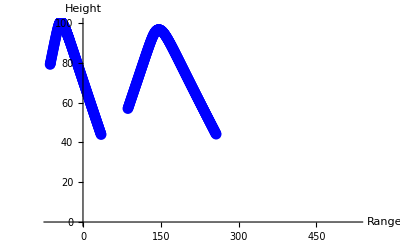

```mathematica
(***************************************************************************)
(***********************   RAY_PATH                **************************)
(***************************************************************************)
(*rayMatrix.wdx is a record of every ray vector in the ray trace computation*)
RayMatrix =Import["rayMatrix.wdx"];
 
lengthMatrix=Length[RayMatrix]
Print ["Length Matrix=",lengthMatrix];

(*        W.wdx is the parameter database                                    *)
WPost=Import["W.wdx"];

(* Will be  alist of height versus range points to plot                      *)
CoordinatesRay={};


(* 
 * Initialize
 *)
PIT2=2.*Pi
PID2=Pi/2.
DEGS=180./Pi
RAD=Pi/180.
CC=2.997925*10^5
K=2.81785E-15*CC^2/Pi

TLON=WPost[[5]]
TLAT=WPost[[4]]
Print ["XMTRH=",XMTRH," PLAT=",PLAT," PLON=",PLON]
Print [" TLAT=",TLAT," TLON=",TLON]
 
 EARTHR=WPost[[2]];  (* Earth Radious Km  *)
  (* lengthMatrix=362;  *) 
For[ii=1,ii< lengthMatrix, ii++,
            Ray=Re[RayMatrix[[ii]] ];


       RayPath[];




] (* End For Loop  *)
Print["Coordinates =",CoordinatesRay];

(*  ListPlot[CoordinatesRay,Joined->True] *)


sfile1=OpenWrite["ray_height_versus_range.txt",FormatType->StandardForm]



For[ii=2,ii<=Length[CoordinatesRay], ii++,
pair=CoordinatesRay[[ii]];
(* Print[pair[[1]]," ", pair[[2]]];*)
Write[sfile1,pair[[1]]," ", pair[[2]]];

]
Close[sfile1];



sfile2=OpenWrite["earth_center_spherical.txt",FormatType->StandardForm]



For[ii=1,ii<lengthMatrix, ii++,
 
 Ray=RayMatrix[[ii]] ;
Write[sfile2,Re[Ray[[1]]]," ",Re[Ray[[2]]]," ",Re[Ray[[3]]]];

]
Close[sfile2];

data=Import["ray_height_versus_range.txt","Table"]

(* Plot the data *)
ListPlot[data,AxesLabel->{"Range","Height"},PlotStyle->Blue,PlotMarkers->Automatic]
```